# Subspace recompilation for BCS Hamiltonian

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

```mathematica
Import["../vqd.wl"]
```

### Modules

```mathematica
GetBlocks::usage="GetBlocks[blockdiagmat_,draw_:True]. Partition indices of a matrix by its blocks.";
GetBlocks[mat_,draw_:True]:=Module[{adjmat,dim=Length@mat,graph},
adjmat=ConstantArray[0,{dim,dim}];
Table[adjmat⟦i,j⟧=If[mat⟦i,j⟧==0,0,1],{i,dim},{j,dim}];
graph=AdjacencyGraph@adjmat;
If[draw,Print@graph];
ConnectedComponents@graph-1
]
```

## BCS simulation

#### Constants

```mathematica
(* non-iteracting harmonic oscillator-type energy levels *)
ϵ=ω(#+0.5)&/@Range[0,4];
(* time-dependent coupling function *)
coupling[t_,g0_,gc_]:=ExpandAll[
(ArcTan[(t-t1)J/(ℏ Γ)]+π/2)(ArcTan[(t2-t)J/(ℏ Γ)]+π/2)(gc-g0)/π^2+g0
]
```

```mathematica
constants={
(* time start to quench and reverse. J is an arbitrary energy unit *)
t1->9 ℏ/J,
t2->18 ℏ/J,
(* initial coupling constant*)
Γ->0.1,
(* frequency *)
ω->5J/3
};
```

```mathematica
(* mean-field eigenvalues *)
Ej[ϵ_,Δ_]:=Sqrt[ϵ^2+Abs[Δ]^2]
(* superconducting gap *)
(*2/g=∑_k 1/Subscript[E, k] tanh[Subscript[E, k]/(2 Subscript[k, b] Temp)]*)
(* since we consider temperature Temp=0, tanh(∞)=1 *)
(* Superconducting gaps*)
Δ0=J;
Δc=2J;
```

```mathematica
g0=2 /Total[1/Ej[ϵ,Δ0]];
gc=2/ Total[1/Ej[ϵ,Δc]];
```

The entire BCS Hamiltonian

```mathematica
Hgaudin[q_,n_,ϵ_,g_]:=Total@Table[({Subscript[X, q],Subscript[Y, q],Subscript[Z, q]}.{Subscript[X, j],Subscript[Y, j],Subscript[Z, j]})/(2(ϵ[[q+1]]-ϵ[[j+1]])), {j,Complement[Range[0,n-1],{q}]}]+Subscript[Z, q]/g
```

```mathematica
HBCS[n_,ϵ_,τ_]:=With[{g=coupling[τ*ℏ/Δ0,g0,gc]/.constants},
SimplifyPaulis@Chop@ExpandAll[
Total@Table[
Simplify[(-g ϵ[[q+1]]+g^2/2)Hgaudin[q,n,ϵ,g]/Δ0/.constants,J>0]
,{q,n-1}]+
SimplifyPaulis@Chop@ExpandAll[SimplifyPaulis@Simplify[g^3/(4Δ0)*(Total@Table[Hgaudin[q,n,ϵ,g],{q,0,n-1}])^2/.constants,J>0]]
]
]
```

#### initial states and memory allocation

```mathematica
(*mean field-eigenvalues*)
ej=Simplify[Ej[ϵ,Δ0]/.constants,J>0];
(* |Subscript[v, j]|^2, |Subscript[u, j]|^2 *)
ujs=Simplify[0.5(1+ϵ/ej)/.constants,J>0];
vjs=Simplify[0.5(1-ϵ/ej)/.constants,J>0];
```

```mathematica
(*  
Subscript[u, j] 0-Subscript[v, j] 1;
Ry[θ]0=Cos[θ/2]0-Sin[θ/2]1 
 *)
θinit=2*ArcCos@Sqrt@ujs;
```

```mathematica
DestroyAllQuregs[]
{ψexact,ψinitexact}=CreateQuregs[5,2];
```

```mathematica
(*exact groundstate*)
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
SetQuregMatrix[ψinitexact,initv];
```

This part (roughly)shows that in the case of exact ground state, the propagators preserves states with hamming weight 1

```mathematica
(*exact groundstate*)
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=List/@eigvec[[First@Ordering[eigval,1]]];
```

Low g(t)

```mathematica
hbcs0mat=CalcPauliStringMatrix[HBCS[5,ϵ,0]]//Chop;
hbcs0mat9=MatrixExp[-ⅈ *0.5*hbcs0mat  ]//Chop;
```

```mathematica
blocks=GetBlocks[hbcs0mat9,False]
```

{{7,11,13,14,19,21,22,25,26,28},{3,5,6,9,10,12,17,18,20,24},{15,23,27,29,30},{1,2,4,8,16},{31},{0}}

```mathematica
(*hamming-weight preserving blocks*)
Table[Length@block->{BaseForm[#,2]&/@block},{block,blocks}]//Column
```

10→{{111_2,1011_2,1101_2,1110_2,10011_2,10101_2,10110_2,11001_2,11010_2,11100_2}}
10→{{11_2,101_2,110_2,1001_2,1010_2,1100_2,10001_2,10010_2,10100_2,11000_2}}
5→{{1111_2,10111_2,11011_2,11101_2,11110_2}}
5→{{1_2,10_2,100_2,1000_2,10000_2}}
1→{{11111_2}}
1→{{0_2}}

```mathematica
CloneQureg[ψmf,ψinitmf];
CloneQureg[ψexact,ψinitexact];
ApplyCircuit[ψmf,Subscript[U, Sequence@@Range[0,4]][hbcs0mat9]];
ApplyCircuit[ψexact,Subscript[U, Sequence@@Range[0,4]][hbcs0mat9]];
```

```mathematica
(* mean-field approximate ground state is bad, and it's all over the place*)
vmf=Chop@GetQuregMatrix@ψmf;
Table[If[vmf[[j]]!=0,{BaseForm[j-1,2],1},{BaseForm[j-1,2],0}],{j,Length@vmf}]
```

{{0_2,1},{1_2,1},{10_2,1},{11_2,1},{100_2,1},{101_2,1},{110_2,1},{111_2,1},{1000_2,1},{1001_2,1},{1010_2,1},{1011_2,1},{1100_2,1},{1101_2,1},{1110_2,1},{1111_2,1},{10000_2,1},{10001_2,1},{10010_2,1},{10011_2,1},{10100_2,1},{10101_2,1},{10110_2,1},{10111_2,1},{11000_2,1},{11001_2,1},{11010_2,1},{11011_2,1},{11100_2,1},{11101_2,1},{11110_2,1},{11111_2,1}}

```mathematica
(* The exact ground state preserves hamming weight 1*)
vex=Chop@GetQuregMatrix@ψexact;
Table[If[vex[[j]]!=0,{BaseForm[j-1,2]},Sequence@@{}],{j,Length@vex}]//Column
```

{1_2}
{10_2}
{100_2}
{1000_2}
{10000_2}

High g(t)

```mathematica
hbcs10=HBCS[5,ϵ,10];
hbcs10mat=CalcPauliStringMatrix[hbcs10]//Chop;
hbcs10mat05=MatrixExp[-ⅈ hbcs10mat 0.5]//Chop;
```

```mathematica
blocks=GetBlocks[hbcs10mat05,False]
```

{{7,11,13,14,19,21,22,25,26,28},{3,5,6,9,10,12,17,18,20,24},{15,23,27,29,30},{1,2,4,8,16},{31},{0}}

```mathematica
ApplyCircuit[ψmf,Subscript[U, Sequence@@Range[0,4]][hbcs10mat05]];
ApplyCircuit[ψexact,Subscript[U, Sequence@@Range[0,4]][hbcs10mat05]];
```

```mathematica
(* Still preserving the ones at high and low g(t)*)
vex=Chop@GetQuregMatrix@ψexact;
Table[If[vex[[j]]!=0,{BaseForm[j-1,2]},Sequence@@{}],{j,Length@vex}]//Column
```

{1_2}
{10_2}
{100_2}
{1000_2}
{10000_2}

#### Obtain the expression ⅇ^(-i δt H_BCS)

```mathematica
(* Medium resolution *)
τs=Sort@DeleteDuplicates@Chop@Join[{0.,4.,8.},Range[8.,20.,0.2],{20.,23.5,27}]
(* the timesteps *)
δτ=Table[τs[[i]]-τs[[i-1]],{i,2,Length@τs}];
PrependTo[δτ,0];
(*sanity check*)
And@@Table[τs[[i]]==Total[δτ[[#]]&/@Range[i]],{i,Length@τs}]
(*τ=t J/ℏ*)
```

{0,4.,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.6,10.8,11.,11.2,11.4,11.6,11.8,12.,12.2,12.4,12.6,12.8,13.,13.2,13.4,13.6,13.8,14.,14.2,14.4,14.6,14.8,15.,15.2,15.4,15.6,15.8,16.,16.2,16.4,16.6,16.8,17.,17.2,17.4,17.6,17.8,18.,18.2,18.4,18.6,18.8,19.,19.2,19.4,19.6,19.8,20.,23.5,27}

True

#### The time-dependent gap Δ is controlled through g(t). Definition of g(t) is here

```mathematica
(*τ=t J/ℏ*)
```

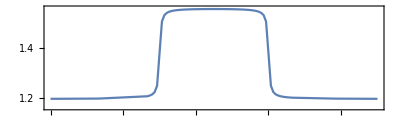

```mathematica
gvals=Simplify[(coupling[#*ℏ/Δ0,g0,gc]/Δ0&/@τs)//.constants,J>0];
ListPlot[Transpose@{τs,gvals},PlotRange->{1.16,1.56},Joined->True,AspectRatio->0.3,Frame->True,FrameTicks->{{Range[1,1.55,0.05],None},{Range[0,27,1],None}}]
```

#### The compilation runs

τ = 0;
bcscompile = {};
Table[
  Print["**** Compile @", DateString[], " τ=", τ, "; δ", δ, " ****"];
  hbcsmat = Chop@MatrixExp[-I *δ*CalcPauliStringMatrix[HBCS[5, ϵ, τ]]]; 
  DestroyAllQuregs[];
  τ += δ;
  conf = DefaultConfig[5, {1, 2, 4, 8, 16}];
  res = CJRecompile[5, hbcsmat, conf];
  AppendTo[bcscompile, {τ, δ, res}];
  
  DumpSave["bcscompile.mx", bcscompile];
  {time, Ecur, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, elimmerge, elimbfsmall, elimmetov, elimbf} = res;
  Print["τ=", τ, "; δ=", δ, "; cost=", Ecur, "; ngates=", Length@ansatz, "; runtime=", time];
  Print@ListPlot[{Elist, Elist}, Joined -> {True, False}, ImageSize -> Small];
  Print@DrawCircuit[ansatz, 5];
  , {δ, δτ[[2 ;;]]}];

**** Compile @Thu 15 Dec 2022 19:11:06 τ=0; δ4. ****

Cycle 1@Thu 15 Dec 2022 19:17:57 completed with ngates=42, cost=2.947008026499276e-6, at eval=1715

Cycle 2@Thu 15 Dec 2022 19:20:21 adjust hyperparams, slowdown:True

Cycle 3@Thu 15 Dec 2022 19:34:23 completed with ngates=51, cost=4.4332561233151324e-7, at eval=4327

Cycle 4@Thu 15 Dec 2022 19:52:53 completed with ngates=62, cost=2.4772069950884656e-8, at eval=6616

Cycle 5@Thu 15 Dec 2022 20:00:19 adjust hyperparams, slowdown:True

Cycle 6@Thu 15 Dec 2022 20:16:55 adjust hyperparams, slowdown:True

Cycle 7@Thu 15 Dec 2022 20:20:57 adjust hyperparams, slowdown:False

Cycle 8@Thu 15 Dec 2022 20:25:18 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=2.47721×10^-8

τ=4.; δ=4.; cost=2.47721×10^-8; ngates=62; runtime=97.6628 min

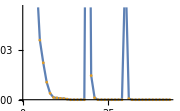

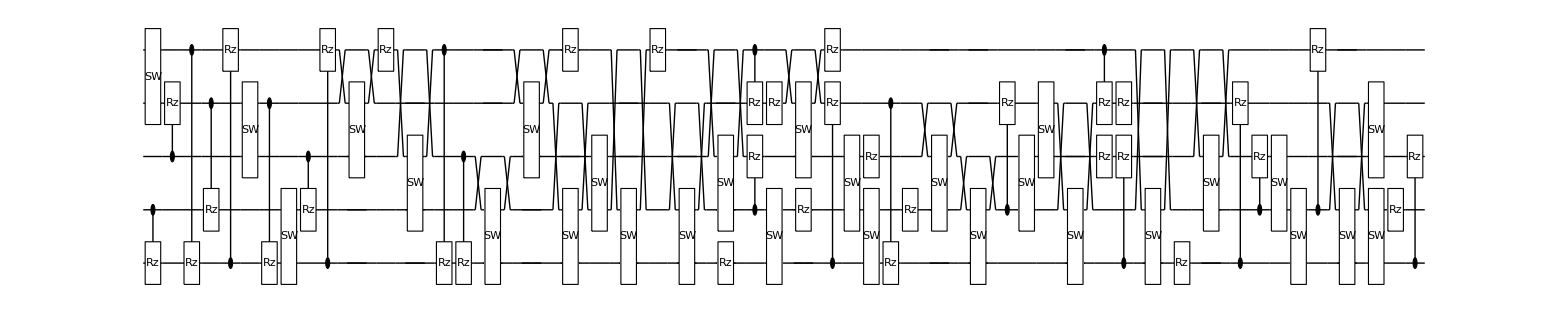

**** Compile @Thu 15 Dec 2022 20:48:46 τ=4.; δ4. ****

Cycle 1@Thu 15 Dec 2022 20:54:34 completed with ngates=35, cost=8.705446470802514e-6, at eval=1706

Cycle 2@Thu 15 Dec 2022 20:56:23 adjust hyperparams, slowdown:True

Cycle 3@Thu 15 Dec 2022 21:05:39 completed with ngates=53, cost=1.1588684541985472e-6, at eval=3858

Cycle 4@Thu 15 Dec 2022 21:22:03 completed with ngates=72, cost=1.5445222578680529e-7, at eval=5784

Cycle 5@Thu 15 Dec 2022 21:48:48 completed with ngates=94, cost=1.8000301582610234e-8, at eval=7964

Cycle 6@Thu 15 Dec 2022 22:00:13 adjust hyperparams, slowdown:True

Cycle 7@Thu 15 Dec 2022 22:24:12 adjust hyperparams, slowdown:True

Cycle 8@Thu 15 Dec 2022 22:30:42 adjust hyperparams, slowdown:False

Cycle 9@Thu 15 Dec 2022 22:37:40 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.80003×10^-8

τ=8.; δ=4.; cost=1.80003×10^-8; ngates=94; runtime=117.49 min

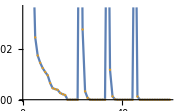

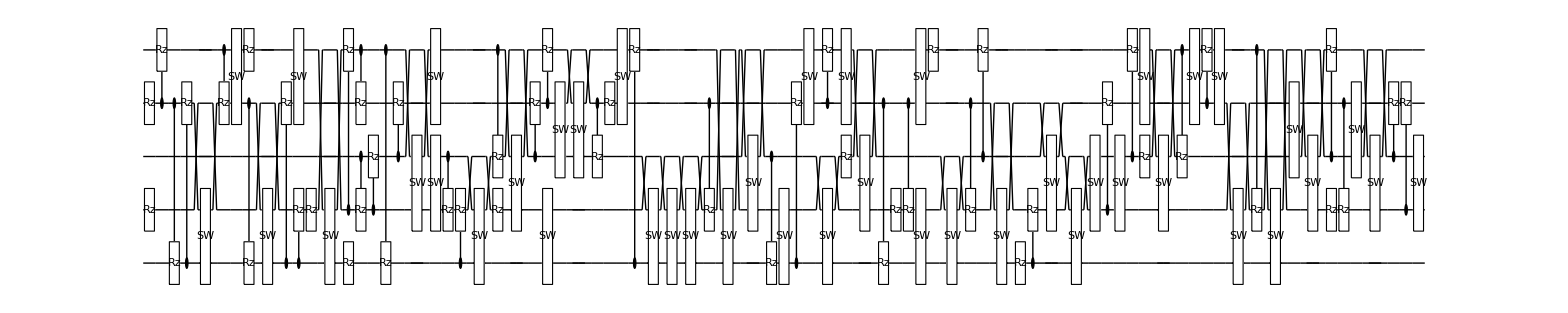

**** Compile @Thu 15 Dec 2022 22:46:22 τ=8.; δ0.2 ****

Cycle 1@Thu 15 Dec 2022 22:51:35 completed with ngates=31, cost=0.0003538152047738441, at eval=1732

Cycle 2@Thu 15 Dec 2022 22:54:33 completed with ngates=34, cost=0.000013242712452621319, at eval=2935

Cycle 3@Thu 15 Dec 2022 22:56:22 adjust hyperparams, slowdown:True

Cycle 4@Thu 15 Dec 2022 23:05:11 completed with ngates=43, cost=5.893423828950972e-7, at eval=5357

Cycle 5@Thu 15 Dec 2022 23:15:54 completed with ngates=60, cost=9.192599625951203e-8, at eval=7018

Cycle 6@Thu 15 Dec 2022 23:22:48 adjust hyperparams, slowdown:True

Cycle 7@Thu 15 Dec 2022 23:38:11 adjust hyperparams, slowdown:True

Cycle 8@Thu 15 Dec 2022 23:41:39 adjust hyperparams, slowdown:False

Cycle 9@Thu 15 Dec 2022 23:45:21 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=9.1926×10^-8

τ=8.2; δ=0.2; cost=9.1926×10^-8; ngates=60; runtime=61.8066 min

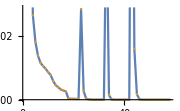

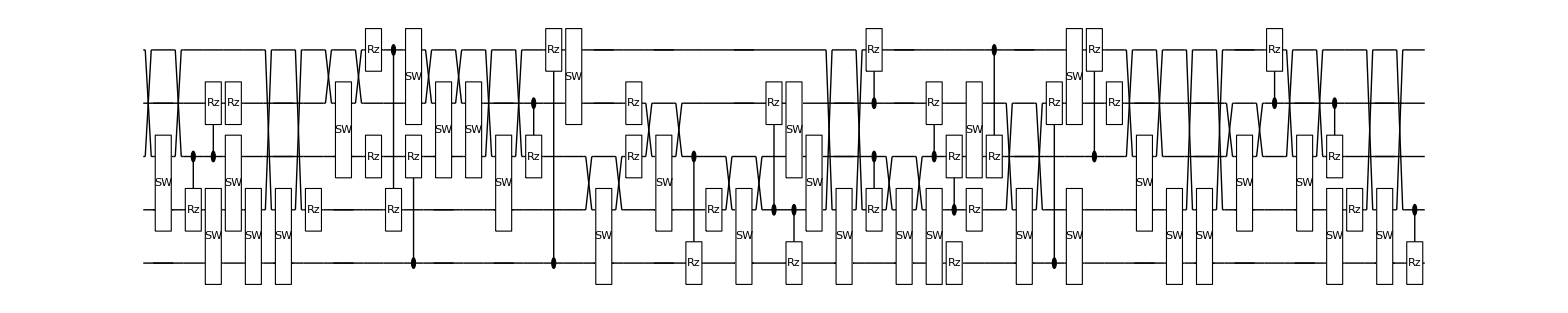

**** Compile @Thu 15 Dec 2022 23:48:16 τ=8.2; δ0.2 ****

Cycle 1@Thu 15 Dec 2022 23:53:57 completed with ngates=34, cost=0.000033447434527822395, at eval=1684

Cycle 2@Thu 15 Dec 2022 23:59:28 completed with ngates=39, cost=1.9002964379843945e-6, at eval=3450

Cycle 3@Fri 16 Dec 2022 00:01:36 adjust hyperparams, slowdown:True

Cycle 4@Fri 16 Dec 2022 00:12:27 completed with ngates=63, cost=9.754805985195958e-8, at eval=5537

Cycle 5@Fri 16 Dec 2022 00:19:26 adjust hyperparams, slowdown:True

ApplyCircuitDerivs::error: Invalid arguments. See ?ApplyCircuitDerivs

General::stop: Further output of ApplyCircuitDerivs::error will be suppressed during this calculation.

Cycle 6@Fri 16 Dec 2022 00:35:37 adjust hyperparams, slowdown:True

Cycle 7@Fri 16 Dec 2022 00:39:26 adjust hyperparams, slowdown:False

Cycle 8@Fri 16 Dec 2022 00:43:19 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=9.75481×10^-8

τ=8.4; δ=0.2; cost=9.75481×10^-8; ngates=63; runtime=57.997 min

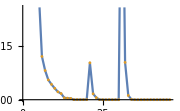

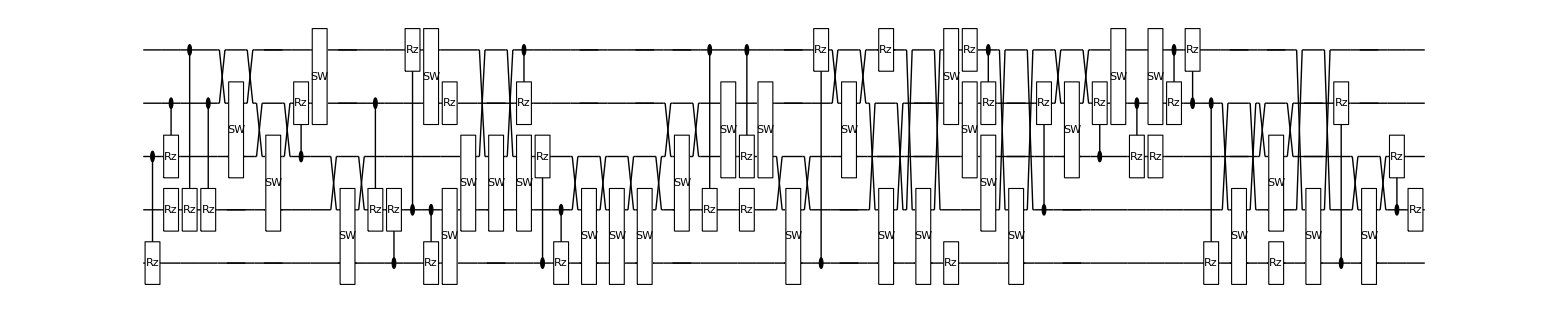

**** Compile @Fri 16 Dec 2022 00:46:22 τ=8.4; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 00:53:14 completed with ngates=51, cost=2.64562463236917e-6, at eval=1607

Cycle 2@Fri 16 Dec 2022 00:56:11 adjust hyperparams, slowdown:True

Cycle 3@Fri 16 Dec 2022 01:01:52 adjust hyperparams, slowdown:True

Cycle 4@Fri 16 Dec 2022 01:15:31 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 01:18:30 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=2.64562×10^-6

τ=8.6; δ=0.2; cost=2.12289×10^-6; ngates=51; runtime=33.7408 min

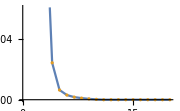

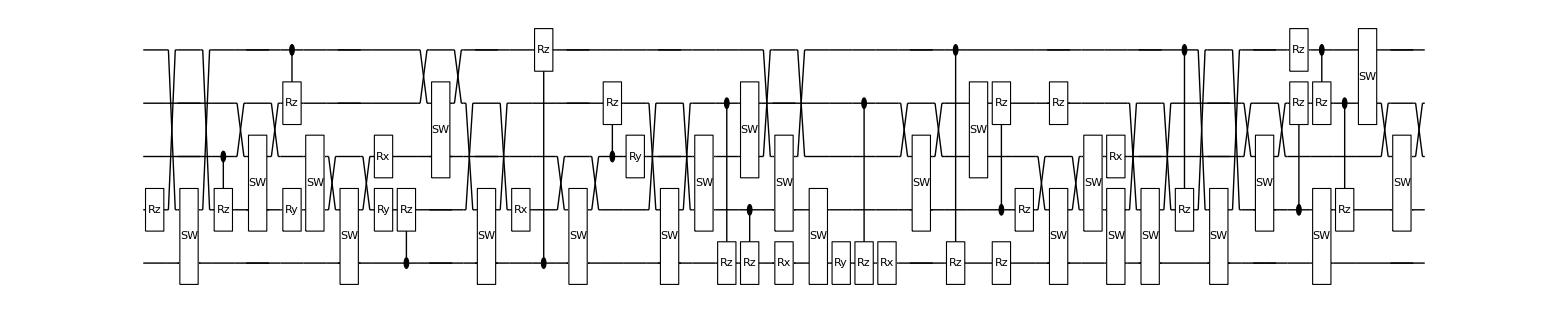

**** Compile @Fri 16 Dec 2022 01:20:13 τ=8.6; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 01:25:30 completed with ngates=42, cost=0.0001378761373466153, at eval=1477

Cycle 2@Fri 16 Dec 2022 01:29:35 completed with ngates=33, cost=0.000026819736095529123, at eval=2840

Cycle 3@Fri 16 Dec 2022 01:31:10 adjust hyperparams, slowdown:True

Cycle 4@Fri 16 Dec 2022 01:38:41 completed with ngates=39, cost=3.404436585863202e-6, at eval=5041

Cycle 5@Fri 16 Dec 2022 01:48:50 completed with ngates=60, cost=2.8256308959306864e-7, at eval=6696

Cycle 6@Fri 16 Dec 2022 01:55:31 adjust hyperparams, slowdown:True

Cycle 7@Fri 16 Dec 2022 02:11:23 adjust hyperparams, slowdown:True

Cycle 8@Fri 16 Dec 2022 02:27:24 completed with ngates=69, cost=4.756276372752666e-8, at eval=10256

Cycle 9@Fri 16 Dec 2022 02:43:20 completed with ngates=81, cost=2.754279593286668e-8, at eval=12020

Cycle 10@Fri 16 Dec 2022 03:06:04 completed with ngates=95, cost=1.9031677456204932e-8, at eval=14003

Cycle 11@Fri 16 Dec 2022 03:12:34 adjust hyperparams, slowdown:False

Cycle 12@Fri 16 Dec 2022 03:19:18 adjust hyperparams, slowdown:False

Cycle 13@Fri 16 Dec 2022 03:26:38 adjust hyperparams, slowdown:False

Cycle 14@Fri 16 Dec 2022 03:55:21 completed with ngates=101, cost=9.631666686438223e-9, at eval=17600

@cycle15, pathetic result.

Cycle 15@Fri 16 Dec 2022 04:03:54 adjust hyperparams, slowdown:False

Cycle 16@Fri 16 Dec 2022 04:36:37 completed with ngates=104, cost=4.0873575635203e-9, at eval=20438

Cycle 17@Fri 16 Dec 2022 05:14:38 completed with ngates=111, cost=2.6679100040283288e-9, at eval=22833

Cycle 18@Fri 16 Dec 2022 05:57:17 completed with ngates=116, cost=4.4996739667624297e-10, at eval=25306

τ=8.8; δ=0.2; cost=4.49967×10^-10; ngates=116; runtime=292.862 min

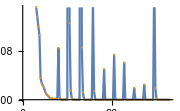

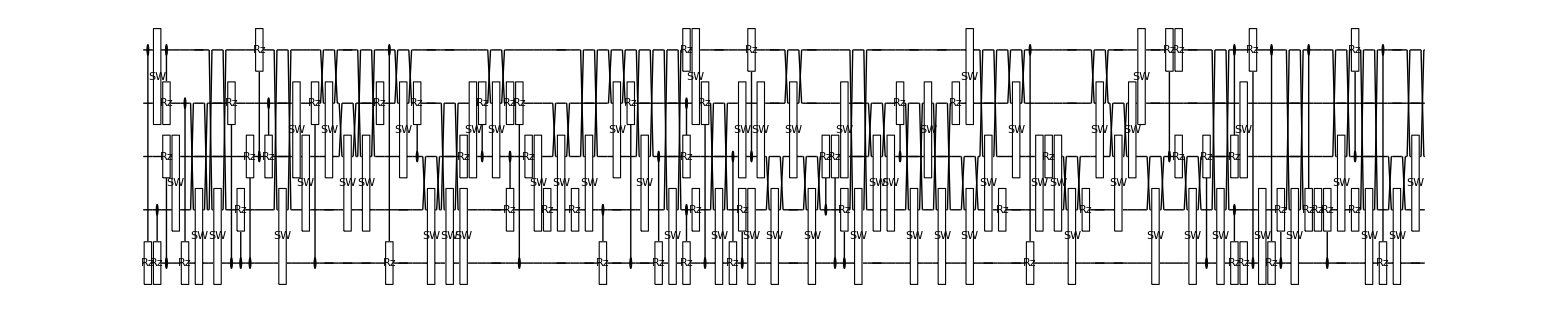

**** Compile @Fri 16 Dec 2022 06:13:11 τ=8.8; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 06:19:04 completed with ngates=40, cost=8.967378830604389e-7, at eval=1682

Cycle 2@Fri 16 Dec 2022 06:21:12 adjust hyperparams, slowdown:True

Cycle 3@Fri 16 Dec 2022 06:25:38 adjust hyperparams, slowdown:True

Cycle 4@Fri 16 Dec 2022 06:36:46 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 06:38:50 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=8.96738×10^-7

τ=9.; δ=0.2; cost=7.39663×10^-7; ngates=40; runtime=26.5438 min

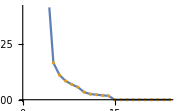

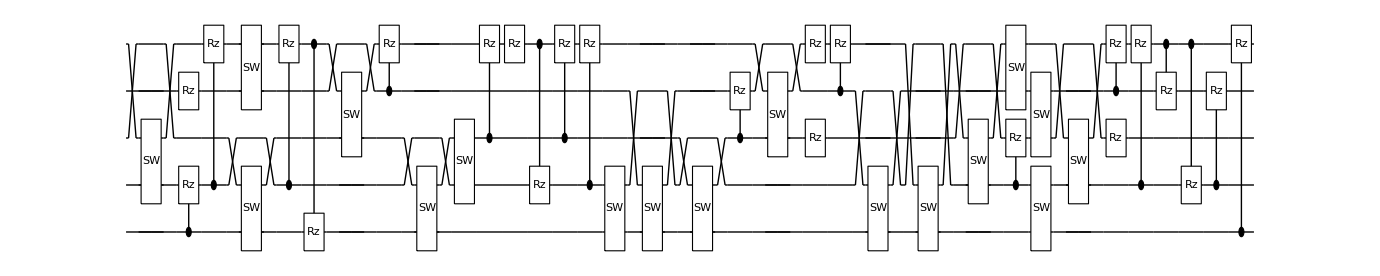

**** Compile @Fri 16 Dec 2022 06:39:49 τ=9.; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 06:45:39 completed with ngates=42, cost=3.7689723451084234e-6, at eval=1528

Cycle 2@Fri 16 Dec 2022 06:47:55 adjust hyperparams, slowdown:True

Cycle 3@Fri 16 Dec 2022 06:58:30 completed with ngates=57, cost=1.6273640546238255e-7, at eval=3599

Cycle 4@Fri 16 Dec 2022 07:05:15 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 07:20:10 adjust hyperparams, slowdown:True

Cycle 6@Fri 16 Dec 2022 07:23:27 adjust hyperparams, slowdown:False

Cycle 7@Fri 16 Dec 2022 07:26:54 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.62736×10^-7

τ=9.2; δ=0.2; cost=1.62736×10^-7; ngates=57; runtime=49.4399 min

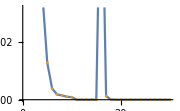

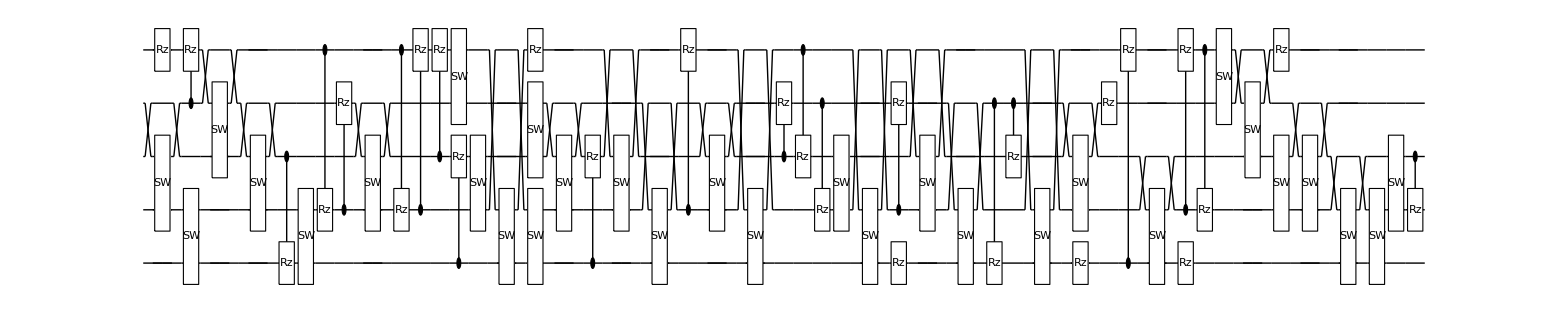

**** Compile @Fri 16 Dec 2022 07:29:22 τ=9.2; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 07:37:00 completed with ngates=40, cost=5.232589668224819e-7, at eval=2202

Cycle 2@Fri 16 Dec 2022 07:39:13 adjust hyperparams, slowdown:True

Cycle 3@Fri 16 Dec 2022 07:51:17 completed with ngates=64, cost=2.979185897977743e-9, at eval=4295

Cycle 4@Fri 16 Dec 2022 07:58:54 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 08:16:09 adjust hyperparams, slowdown:True

Cycle 6@Fri 16 Dec 2022 08:20:13 adjust hyperparams, slowdown:False

Cycle 7@Fri 16 Dec 2022 08:24:22 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=2.97919×10^-9

τ=9.4; δ=0.2; cost=2.97919×10^-9; ngates=64; runtime=58.4111 min

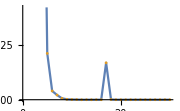

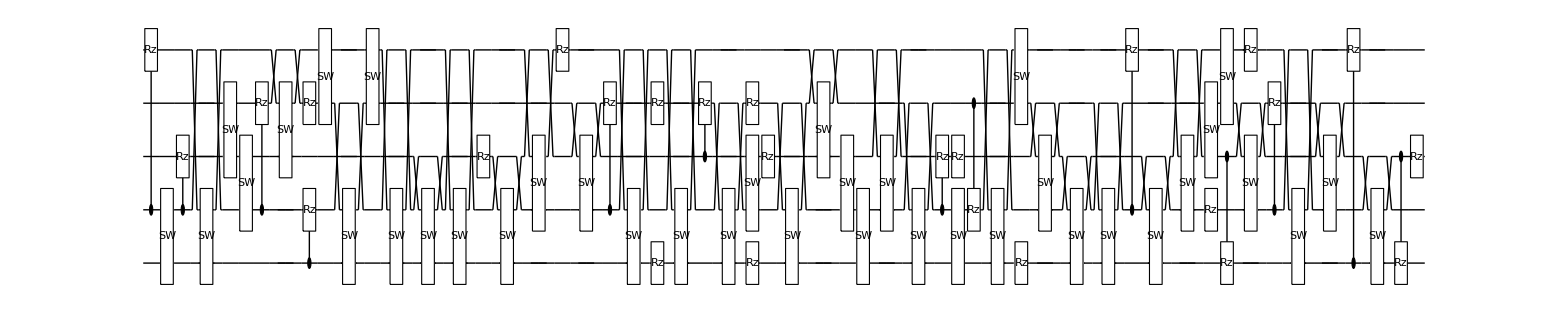

**** Compile @Fri 16 Dec 2022 08:27:53 τ=9.4; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 08:35:50 completed with ngates=50, cost=8.654403237384756e-7, at eval=1871

Cycle 2@Fri 16 Dec 2022 08:38:33 adjust hyperparams, slowdown:True

Cycle 3@Fri 16 Dec 2022 08:44:00 adjust hyperparams, slowdown:True

Cycle 4@Fri 16 Dec 2022 08:57:12 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 09:00:02 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=8.6544×10^-7

τ=9.6; δ=0.2; cost=8.6544×10^-7; ngates=50; runtime=34.1201 min

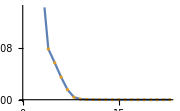

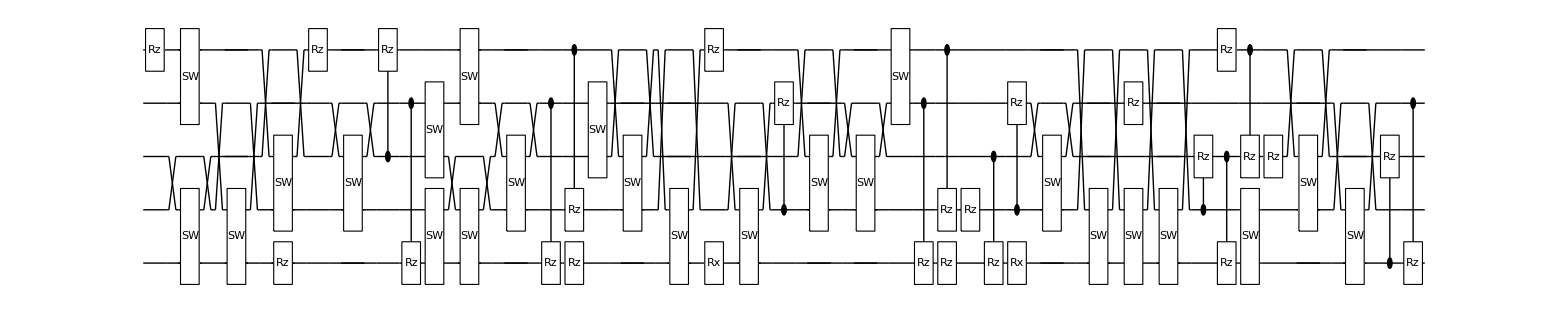

**** Compile @Fri 16 Dec 2022 09:02:06 τ=9.6; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 09:08:01 completed with ngates=37, cost=1.1446651030366795e-6, at eval=1510

Cycle 2@Fri 16 Dec 2022 09:14:24 completed with ngates=52, cost=6.144624474790916e-7, at eval=2913

Cycle 3@Fri 16 Dec 2022 09:24:00 completed with ngates=65, cost=5.796246438372066e-8, at eval=4455

Cycle 4@Fri 16 Dec 2022 09:27:41 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 09:34:59 adjust hyperparams, slowdown:True

Cycle 6@Fri 16 Dec 2022 09:51:51 adjust hyperparams, slowdown:True

Cycle 7@Fri 16 Dec 2022 09:55:38 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=5.79625×10^-8

τ=9.8; δ=0.2; cost=5.79625×10^-8; ngates=65; runtime=56.8412 min

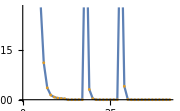

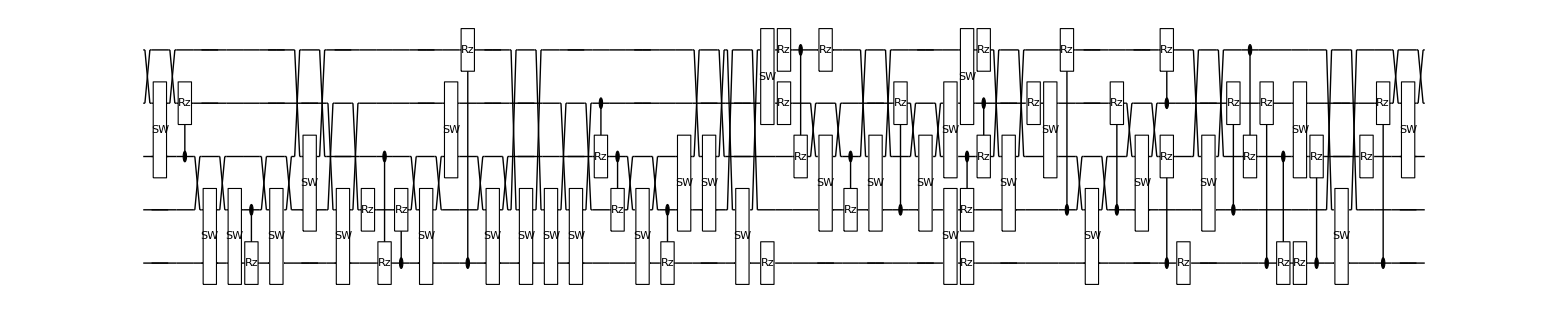

**** Compile @Fri 16 Dec 2022 09:59:03 τ=9.8; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 10:04:21 completed with ngates=32, cost=0.00003090614438772121, at eval=1680

Cycle 2@Fri 16 Dec 2022 10:08:55 completed with ngates=38, cost=5.547322535992549e-6, at eval=3191

Cycle 3@Fri 16 Dec 2022 10:14:52 completed with ngates=50, cost=1.1755858260187324e-6, at eval=4711

Cycle 4@Fri 16 Dec 2022 10:23:47 completed with ngates=63, cost=2.2559985934922366e-7, at eval=6289

Cycle 5@Fri 16 Dec 2022 10:37:58 completed with ngates=79, cost=5.721933216129571e-8, at eval=8068

Cycle 6@Fri 16 Dec 2022 10:42:34 adjust hyperparams, slowdown:True

Cycle 7@Fri 16 Dec 2022 10:51:04 adjust hyperparams, slowdown:True

Cycle 8@Fri 16 Dec 2022 11:11:58 adjust hyperparams, slowdown:True

Cycle 9@Fri 16 Dec 2022 11:17:33 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=5.72193×10^-8

τ=10.; δ=0.2; cost=5.72193×10^-8; ngates=79; runtime=86.7073 min

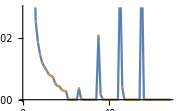

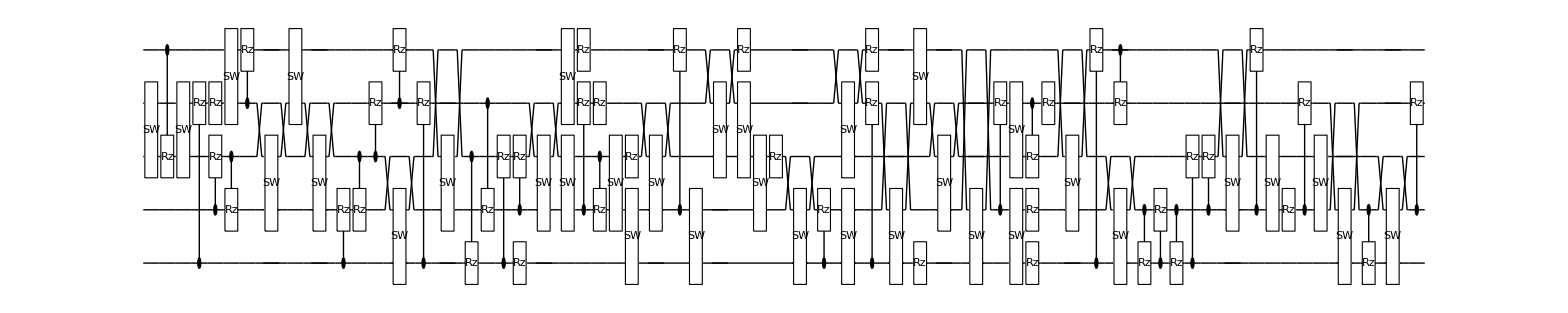

**** Compile @Fri 16 Dec 2022 11:25:51 τ=10.; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 11:32:35 completed with ngates=41, cost=1.5208053063542337e-6, at eval=1697

Cycle 2@Fri 16 Dec 2022 11:35:05 adjust hyperparams, slowdown:True

Cycle 3@Fri 16 Dec 2022 11:40:13 adjust hyperparams, slowdown:True

Cycle 4@Fri 16 Dec 2022 12:05:54 completed with ngates=51, cost=2.5002078785085757e-7, at eval=5623

Cycle 5@Fri 16 Dec 2022 12:51:38 completed with ngates=85, cost=1.0096556590788452e-8, at eval=8643

Cycle 6@Fri 16 Dec 2022 13:16:01 adjust hyperparams, slowdown:True

Cycle 7@Fri 16 Dec 2022 13:23:03 adjust hyperparams, slowdown:False

Cycle 8@Fri 16 Dec 2022 13:30:19 adjust hyperparams, slowdown:False

@cycle9, pathetic result.

Cycle 9@Fri 16 Dec 2022 13:38:08 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.00966×10^-8

τ=10.2; δ=0.2; cost=1.00966×10^-8; ngates=85; runtime=177.807 min

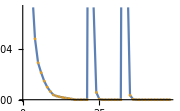

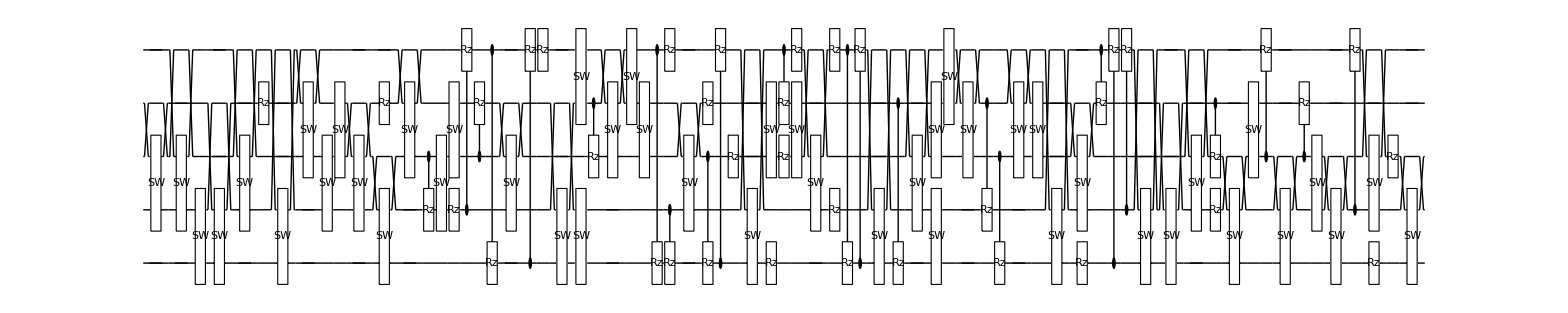

**** Compile @Fri 16 Dec 2022 14:23:41 τ=10.2; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 14:30:40 completed with ngates=39, cost=0.000011705352734869834, at eval=1744

Cycle 2@Fri 16 Dec 2022 14:38:04 completed with ngates=49, cost=2.5346919642066368e-6, at eval=3256

Cycle 3@Fri 16 Dec 2022 14:52:26 completed with ngates=60, cost=7.349336426099029e-7, at eval=5481

Cycle 4@Fri 16 Dec 2022 15:05:13 completed with ngates=67, cost=7.610911345601323e-8, at eval=7091

Cycle 5@Fri 16 Dec 2022 15:09:24 adjust hyperparams, slowdown:True

Cycle 6@Fri 16 Dec 2022 15:17:15 adjust hyperparams, slowdown:True

Cycle 7@Fri 16 Dec 2022 15:33:34 adjust hyperparams, slowdown:True

Cycle 8@Fri 16 Dec 2022 15:37:12 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=7.61091×10^-8

τ=10.4; δ=0.2; cost=7.61091×10^-8; ngates=67; runtime=93.6766 min

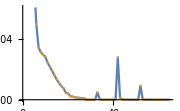

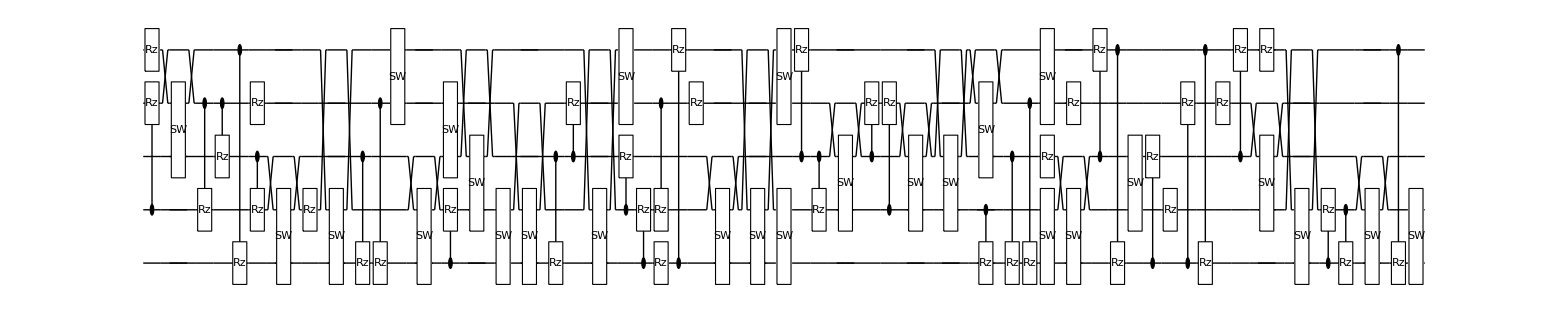

**** Compile @Fri 16 Dec 2022 15:57:28 τ=10.4; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 16:03:59 completed with ngates=42, cost=4.0765255016061985e-7, at eval=1708

Cycle 2@Fri 16 Dec 2022 16:06:15 adjust hyperparams, slowdown:True

Cycle 3@Fri 16 Dec 2022 16:11:00 adjust hyperparams, slowdown:True

Cycle 4@Fri 16 Dec 2022 16:23:06 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 16:25:30 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=4.07653×10^-7

τ=10.6; δ=0.2; cost=4.07653×10^-7; ngates=42; runtime=29.336 min

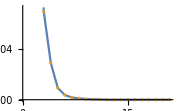

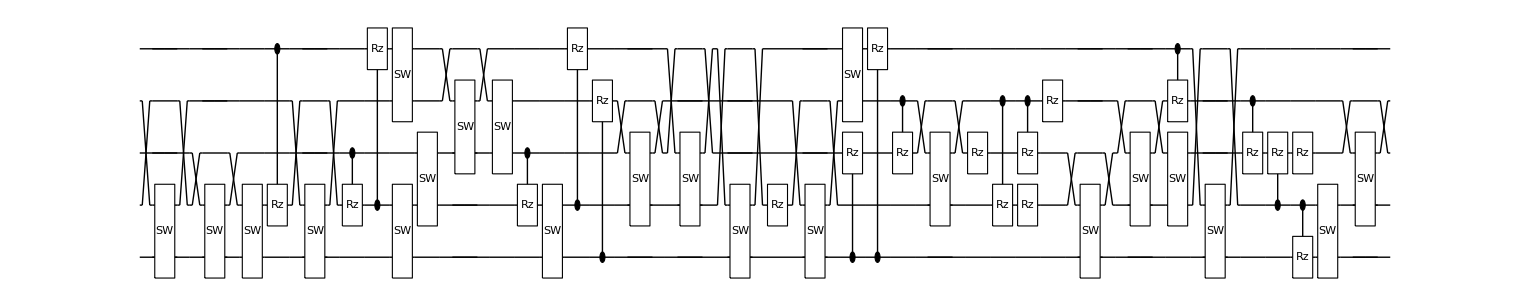

**** Compile @Fri 16 Dec 2022 16:26:54 τ=10.6; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 16:33:41 completed with ngates=44, cost=7.89635356102103e-7, at eval=1672

Cycle 2@Fri 16 Dec 2022 16:42:59 completed with ngates=54, cost=3.914858561770984e-7, at eval=3537

Cycle 3@Fri 16 Dec 2022 16:53:58 completed with ngates=70, cost=5.994050278346208e-8, at eval=5105

Cycle 4@Fri 16 Dec 2022 16:58:08 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 17:06:13 adjust hyperparams, slowdown:True

Cycle 6@Fri 16 Dec 2022 17:24:03 adjust hyperparams, slowdown:True

Cycle 7@Fri 16 Dec 2022 17:28:26 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=5.99405×10^-8

τ=10.8; δ=0.2; cost=5.99405×10^-8; ngates=70; runtime=65.4742 min

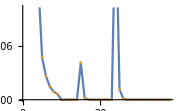

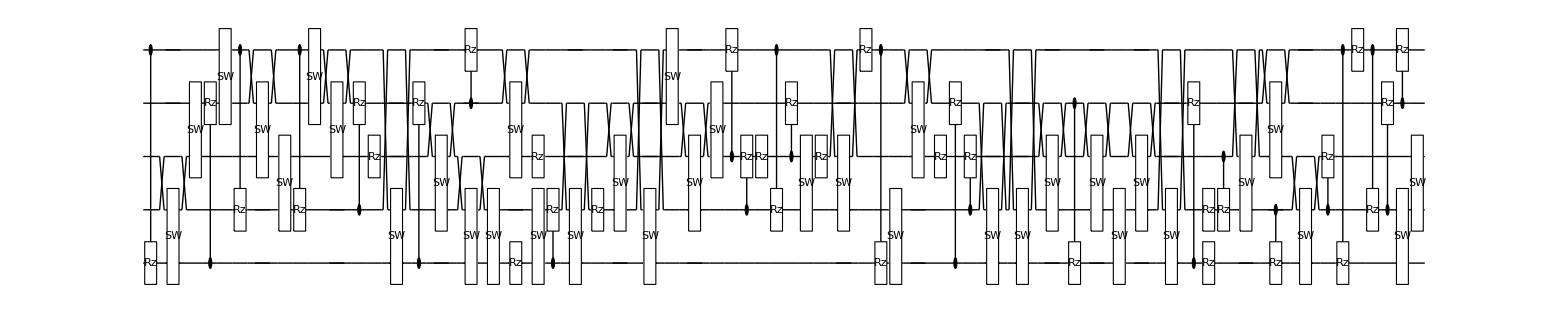

**** Compile @Fri 16 Dec 2022 17:32:29 τ=10.8; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 17:39:25 completed with ngates=36, cost=2.2234540028032157e-6, at eval=2143

Cycle 2@Fri 16 Dec 2022 17:41:19 adjust hyperparams, slowdown:True

Cycle 3@Fri 16 Dec 2022 17:45:27 adjust hyperparams, slowdown:True

Cycle 4@Fri 16 Dec 2022 17:56:10 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 17:58:13 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=2.22345×10^-6

τ=11.; δ=0.2; cost=1.78035×10^-6; ngates=36; runtime=26.5135 min

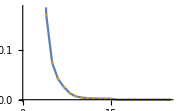

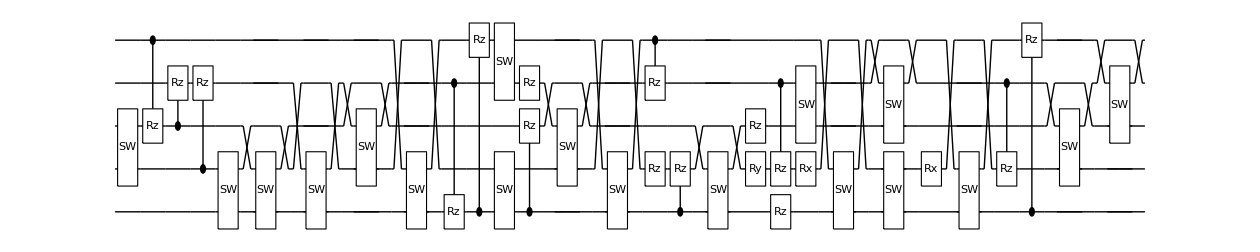

**** Compile @Fri 16 Dec 2022 17:59:06 τ=11.; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 18:04:34 completed with ngates=36, cost=0.000024872867977254742, at eval=1587

Cycle 2@Fri 16 Dec 2022 18:09:27 completed with ngates=43, cost=8.931157809977108e-7, at eval=2921

Cycle 3@Fri 16 Dec 2022 18:16:07 completed with ngates=54, cost=5.4731941867558476e-8, at eval=4267

Cycle 4@Fri 16 Dec 2022 18:18:59 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 18:37:29 completed with ngates=84, cost=1.9127166517307614e-9, at eval=6616

Cycle 6@Fri 16 Dec 2022 18:47:06 adjust hyperparams, slowdown:True

Cycle 7@Fri 16 Dec 2022 19:07:44 adjust hyperparams, slowdown:True

Cycle 8@Fri 16 Dec 2022 19:13:02 adjust hyperparams, slowdown:False

Cycle 9@Fri 16 Dec 2022 19:18:28 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.91272×10^-9

τ=11.2; δ=0.2; cost=1.91272×10^-9; ngates=84; runtime=85.3534 min

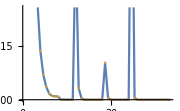

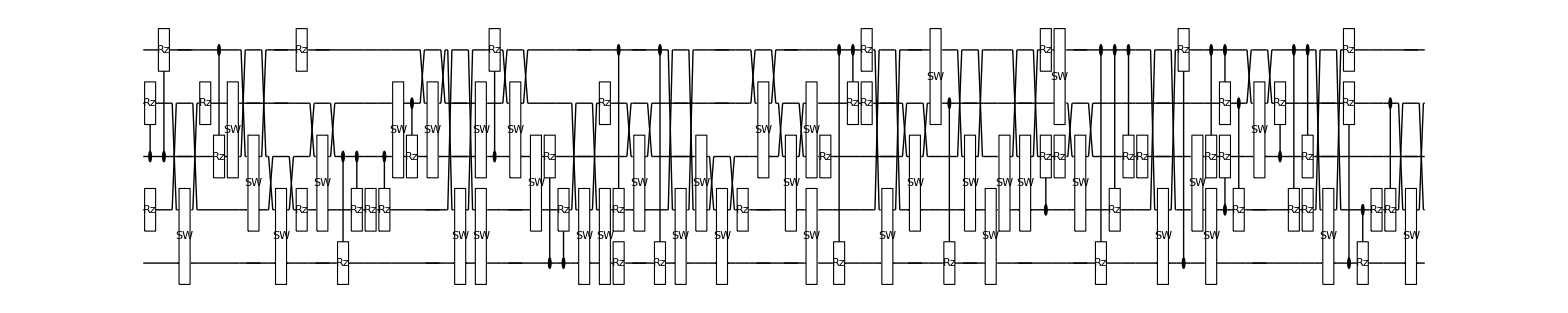

**** Compile @Fri 16 Dec 2022 19:24:33 τ=11.2; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 19:31:06 completed with ngates=49, cost=4.752888625114693e-6, at eval=1671

Cycle 2@Fri 16 Dec 2022 19:33:45 adjust hyperparams, slowdown:True

Cycle 3@Fri 16 Dec 2022 19:39:10 adjust hyperparams, slowdown:True

Cycle 4@Fri 16 Dec 2022 19:51:48 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 19:59:11 completed with ngates=52, cost=7.671552133547976e-7, at eval=5039

Cycle 6@Fri 16 Dec 2022 20:02:13 adjust hyperparams, slowdown:False

Cycle 7@Fri 16 Dec 2022 20:05:19 adjust hyperparams, slowdown:False

Cycle 8@Fri 16 Dec 2022 20:08:34 adjust hyperparams, slowdown:False

Cycle 9@Fri 16 Dec 2022 20:11:53 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=7.67155×10^-7

τ=11.4; δ=0.2; cost=7.67155×10^-7; ngates=52; runtime=49.4347 min

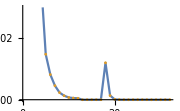

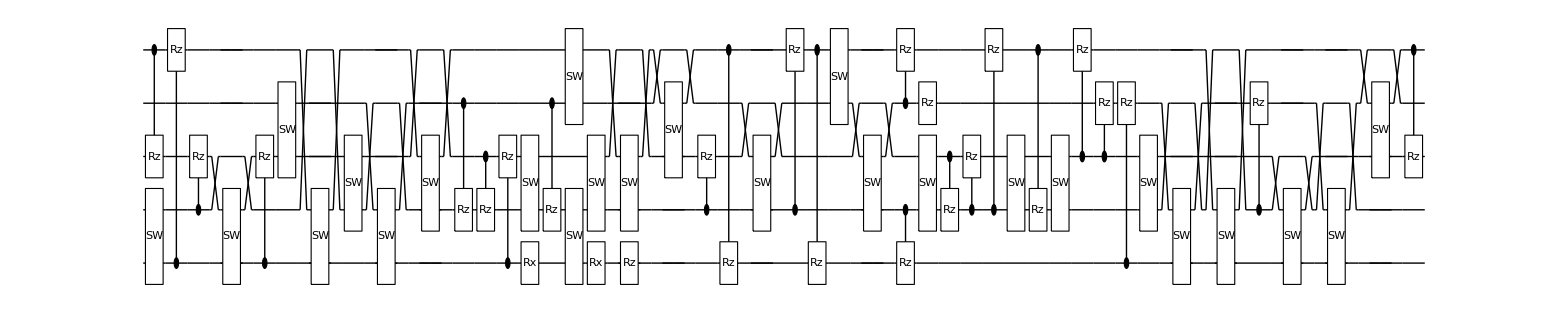

**** Compile @Fri 16 Dec 2022 20:14:05 τ=11.4; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 20:20:48 completed with ngates=43, cost=0.0001794331596468579, at eval=2142

Cycle 2@Fri 16 Dec 2022 20:28:04 completed with ngates=32, cost=0.00009633561466859675, at eval=5060

Cycle 3@Fri 16 Dec 2022 20:32:05 completed with ngates=37, cost=0.000011665248434766795, at eval=6681

Cycle 4@Fri 16 Dec 2022 20:33:56 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 20:41:33 completed with ngates=42, cost=1.1009230005409876e-6, at eval=8773

Cycle 6@Fri 16 Dec 2022 20:46:17 adjust hyperparams, slowdown:True

Cycle 7@Fri 16 Dec 2022 20:58:08 adjust hyperparams, slowdown:True

Cycle 8@Fri 16 Dec 2022 21:04:50 completed with ngates=52, cost=1.9482225588340896e-7, at eval=11575

Cycle 9@Fri 16 Dec 2022 21:13:43 completed with ngates=61, cost=4.19212724533935e-8, at eval=13146

Cycle 10@Fri 16 Dec 2022 21:17:08 adjust hyperparams, slowdown:False

Cycle 11@Fri 16 Dec 2022 21:20:44 adjust hyperparams, slowdown:False

Cycle 12@Fri 16 Dec 2022 21:24:27 adjust hyperparams, slowdown:False

Cycle 13@Fri 16 Dec 2022 21:28:12 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=4.19213×10^-8

τ=11.6; δ=0.2; cost=4.19213×10^-8; ngates=61; runtime=77.0651 min

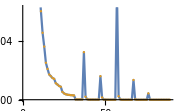

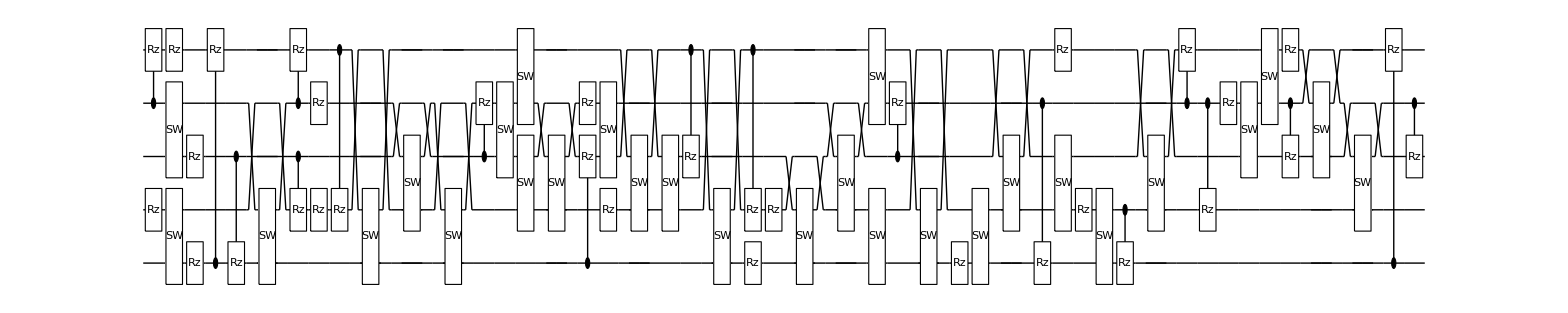

**** Compile @Fri 16 Dec 2022 21:31:15 τ=11.6; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 21:37:03 completed with ngates=36, cost=4.993449788104343e-7, at eval=1740

Cycle 2@Fri 16 Dec 2022 21:38:54 adjust hyperparams, slowdown:True

Cycle 3@Fri 16 Dec 2022 21:50:06 completed with ngates=67, cost=4.1191263733253436e-8, at eval=3960

Cycle 4@Fri 16 Dec 2022 21:57:09 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 22:13:56 adjust hyperparams, slowdown:True

Cycle 6@Fri 16 Dec 2022 22:17:47 adjust hyperparams, slowdown:False

Cycle 7@Fri 16 Dec 2022 22:21:39 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=4.11913×10^-8

τ=11.8; δ=0.2; cost=4.11913×10^-8; ngates=67; runtime=53.9446 min

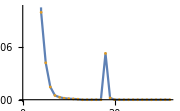

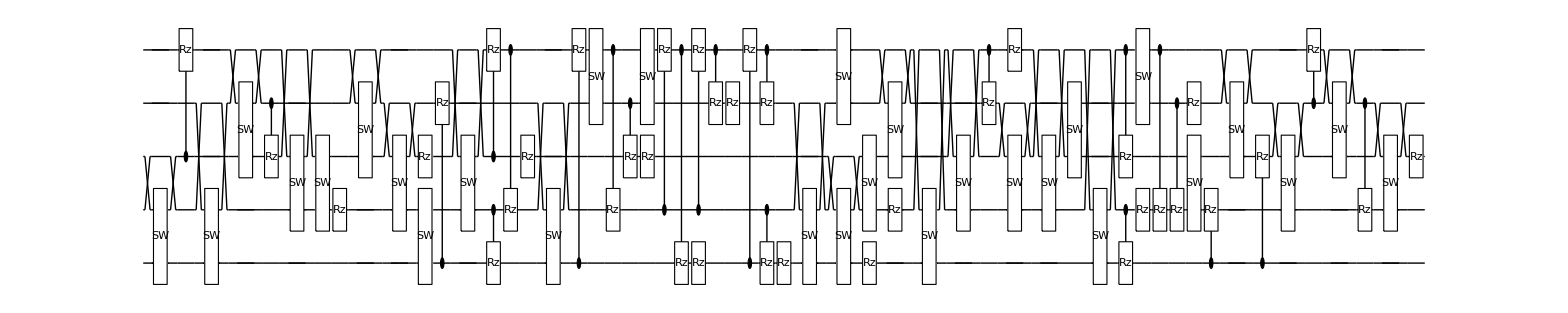

**** Compile @Fri 16 Dec 2022 22:25:18 τ=11.8; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 22:31:23 completed with ngates=43, cost=3.654776092210099e-6, at eval=1600

Cycle 2@Fri 16 Dec 2022 22:33:42 adjust hyperparams, slowdown:True

Cycle 3@Fri 16 Dec 2022 22:45:18 completed with ngates=52, cost=4.4597336457119496e-7, at eval=4077

Cycle 4@Fri 16 Dec 2022 22:50:56 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 23:04:53 adjust hyperparams, slowdown:True

Cycle 6@Fri 16 Dec 2022 23:16:18 completed with ngates=59, cost=3.041737683950885e-8, at eval=7480

Cycle 7@Fri 16 Dec 2022 23:19:41 adjust hyperparams, slowdown:False

Cycle 8@Fri 16 Dec 2022 23:23:16 adjust hyperparams, slowdown:False

Cycle 9@Fri 16 Dec 2022 23:26:56 adjust hyperparams, slowdown:False

Cycle 10@Fri 16 Dec 2022 23:30:40 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=3.04174×10^-8

τ=12.; δ=0.2; cost=3.04174×10^-8; ngates=59; runtime=68.1541 min

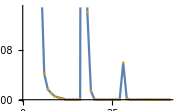

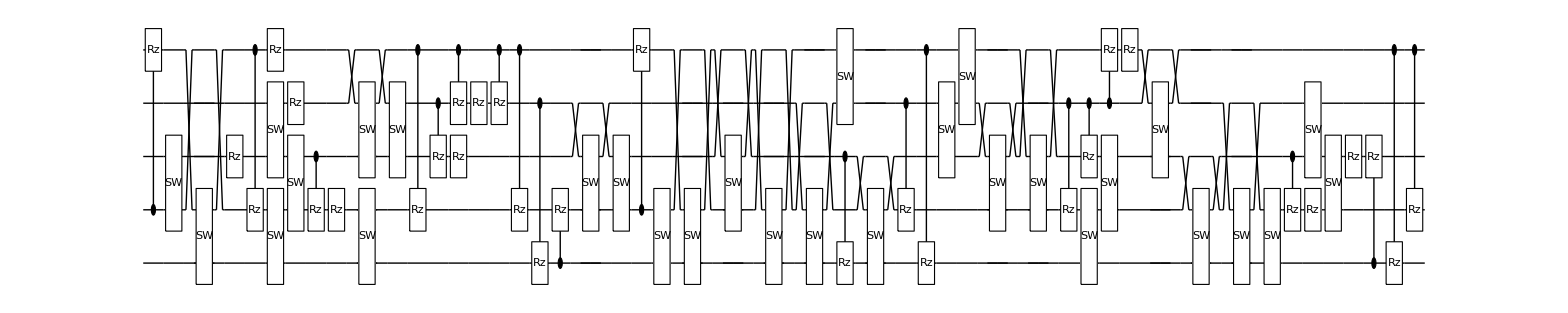

**** Compile @Fri 16 Dec 2022 23:33:34 τ=12.; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 23:41:41 completed with ngates=57, cost=1.1807844663147549e-6, at eval=1868

Cycle 2@Fri 16 Dec 2022 23:44:36 adjust hyperparams, slowdown:True

Cycle 3@Fri 16 Dec 2022 23:50:35 adjust hyperparams, slowdown:True

Cycle 4@Sat 17 Dec 2022 00:03:41 adjust hyperparams, slowdown:True

Cycle 5@Sat 17 Dec 2022 00:06:40 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.18078×10^-6

τ=12.2; δ=0.2; cost=1.18078×10^-6; ngates=57; runtime=35.0679 min

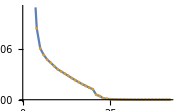

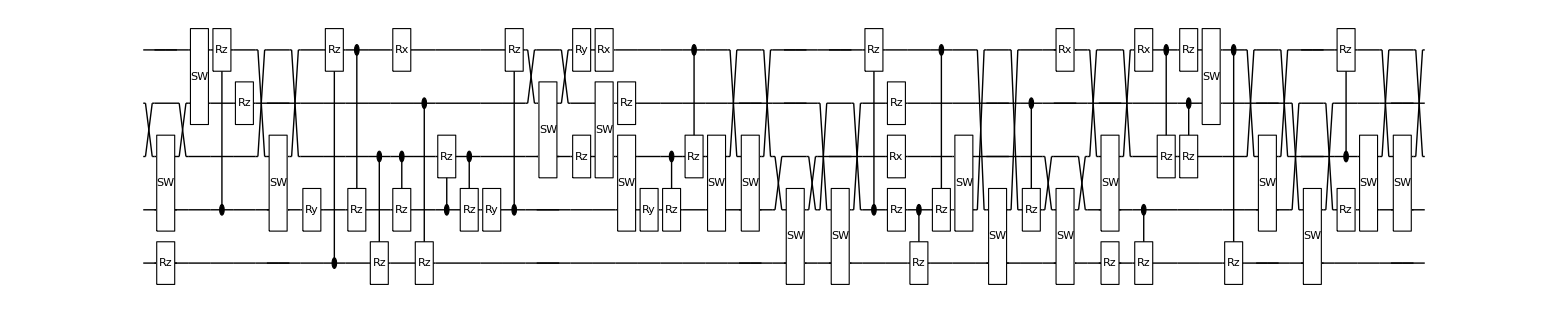

**** Compile @Sat 17 Dec 2022 00:08:44 τ=12.2; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 00:16:30 completed with ngates=40, cost=1.721929682174661e-7, at eval=2373

Cycle 2@Sat 17 Dec 2022 00:18:34 adjust hyperparams, slowdown:True

Cycle 3@Sat 17 Dec 2022 00:22:58 adjust hyperparams, slowdown:True

Cycle 4@Sat 17 Dec 2022 00:34:11 adjust hyperparams, slowdown:True

Cycle 5@Sat 17 Dec 2022 00:36:20 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.72193×10^-7

τ=12.4; δ=0.2; cost=1.72193×10^-7; ngates=40; runtime=28.8881 min

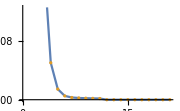

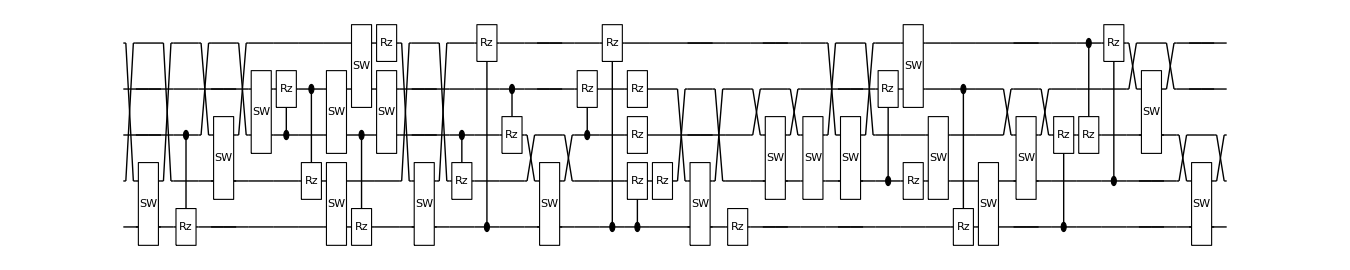

**** Compile @Sat 17 Dec 2022 00:37:43 τ=12.4; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 00:43:59 completed with ngates=42, cost=0.000020361846328587063, at eval=1781

Cycle 2@Sat 17 Dec 2022 00:46:10 adjust hyperparams, slowdown:True

Cycle 3@Sat 17 Dec 2022 00:55:03 completed with ngates=47, cost=3.7180708734041445e-6, at eval=3873

Cycle 4@Sat 17 Dec 2022 01:04:46 completed with ngates=47, cost=2.8790385808719066e-7, at eval=5479

Cycle 5@Sat 17 Dec 2022 01:09:53 adjust hyperparams, slowdown:True

Cycle 6@Sat 17 Dec 2022 01:22:39 adjust hyperparams, slowdown:True

Cycle 7@Sat 17 Dec 2022 01:25:12 adjust hyperparams, slowdown:False

Cycle 8@Sat 17 Dec 2022 01:27:56 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=2.87904×10^-7

τ=12.6; δ=0.2; cost=2.87904×10^-7; ngates=47; runtime=51.7547 min

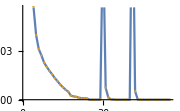

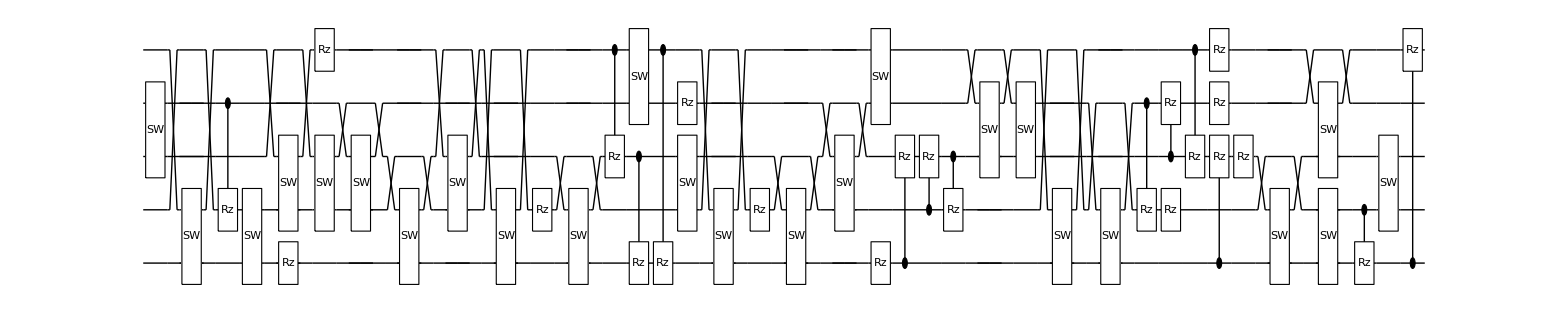

**** Compile @Sat 17 Dec 2022 01:29:35 τ=12.6; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 01:36:40 completed with ngates=38, cost=3.862560644773971e-6, at eval=2147

Cycle 2@Sat 17 Dec 2022 01:41:33 completed with ngates=44, cost=1.1938692821011898e-6, at eval=3461

Cycle 3@Sat 17 Dec 2022 01:48:54 completed with ngates=56, cost=3.0712583698466744e-7, at eval=4945

Cycle 4@Sat 17 Dec 2022 01:59:44 completed with ngates=69, cost=9.829748792711257e-9, at eval=6527

Cycle 5@Sat 17 Dec 2022 02:03:46 adjust hyperparams, slowdown:True

Cycle 6@Sat 17 Dec 2022 02:11:33 adjust hyperparams, slowdown:True

Cycle 7@Sat 17 Dec 2022 02:29:24 adjust hyperparams, slowdown:True

Cycle 8@Sat 17 Dec 2022 02:33:33 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=9.82975×10^-9

τ=12.8; δ=0.2; cost=9.82975×10^-9; ngates=69; runtime=67.7956 min

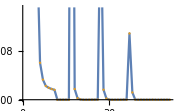

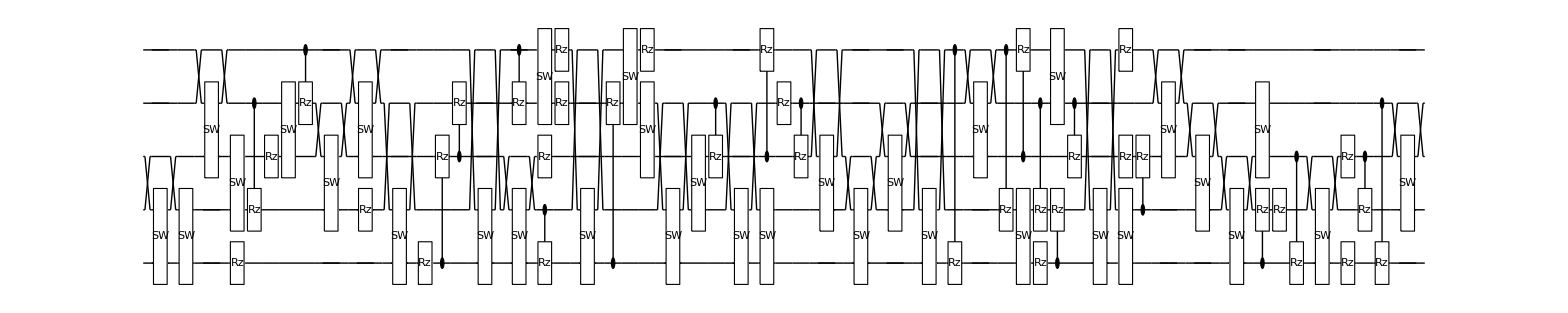

**** Compile @Sat 17 Dec 2022 02:37:29 τ=12.8; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 02:42:20 completed with ngates=34, cost=0.000015174749367186102, at eval=1424

Cycle 2@Sat 17 Dec 2022 02:46:59 completed with ngates=46, cost=4.939152881133779e-7, at eval=2806

Cycle 3@Sat 17 Dec 2022 02:49:24 adjust hyperparams, slowdown:True

Cycle 4@Sat 17 Dec 2022 03:01:51 completed with ngates=68, cost=5.319780171930688e-9, at eval=5014

Cycle 5@Sat 17 Dec 2022 03:09:18 adjust hyperparams, slowdown:True

Cycle 6@Sat 17 Dec 2022 03:26:23 adjust hyperparams, slowdown:True

Cycle 7@Sat 17 Dec 2022 03:30:15 adjust hyperparams, slowdown:False

Cycle 8@Sat 17 Dec 2022 03:34:19 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=5.31978×10^-9

τ=13.; δ=0.2; cost=5.31978×10^-9; ngates=68; runtime=60.3742 min

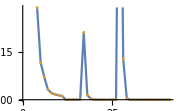

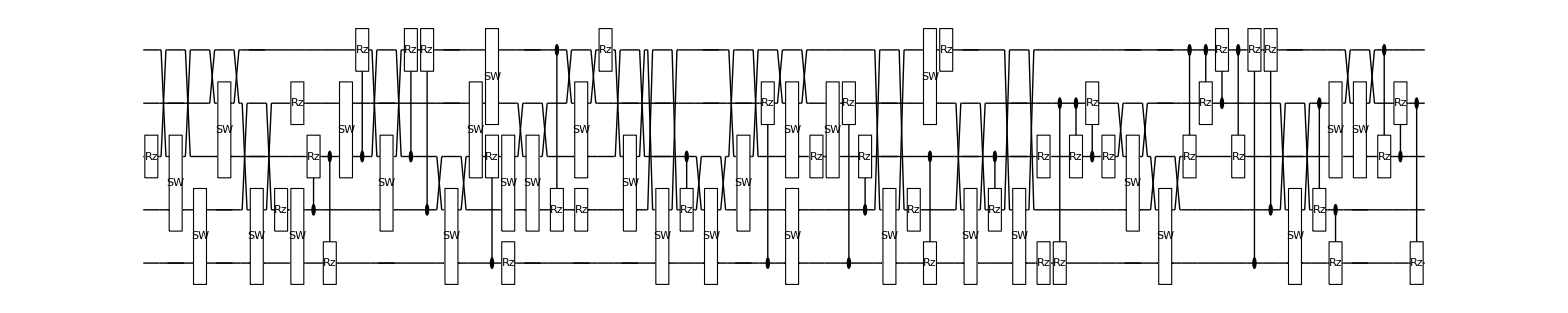

**** Compile @Sat 17 Dec 2022 03:37:58 τ=13.; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 03:44:47 completed with ngates=46, cost=8.063011687209354e-7, at eval=1810

Cycle 2@Sat 17 Dec 2022 03:47:15 adjust hyperparams, slowdown:True

Cycle 3@Sat 17 Dec 2022 03:52:10 adjust hyperparams, slowdown:True

Cycle 4@Sat 17 Dec 2022 04:04:35 adjust hyperparams, slowdown:True

Cycle 5@Sat 17 Dec 2022 04:07:04 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=8.06301×10^-7

τ=13.2; δ=0.2; cost=7.10932×10^-7; ngates=46; runtime=30.5416 min

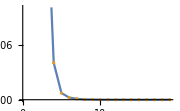

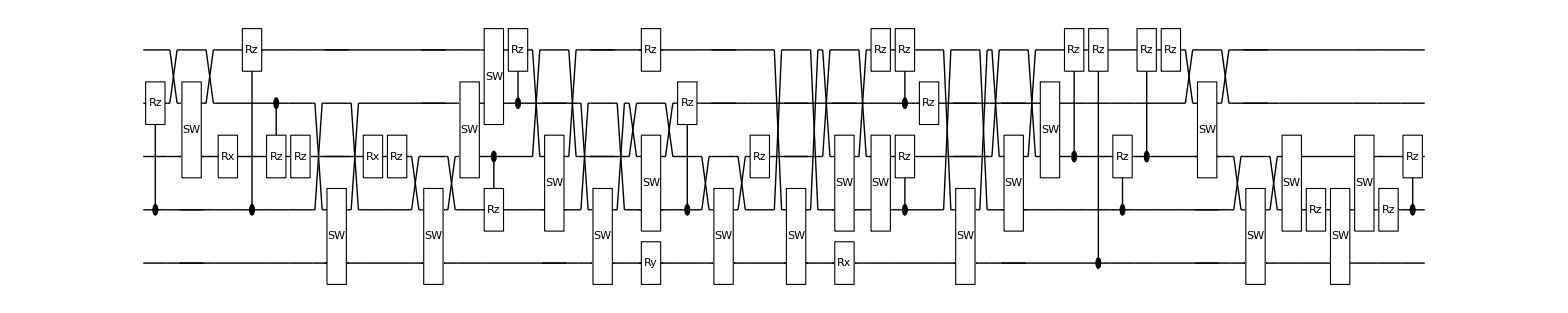

**** Compile @Sat 17 Dec 2022 04:08:36 τ=13.2; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 04:14:47 completed with ngates=39, cost=3.0885707287264808e-6, at eval=1864

Cycle 2@Sat 17 Dec 2022 04:16:52 adjust hyperparams, slowdown:True

Cycle 3@Sat 17 Dec 2022 04:21:09 adjust hyperparams, slowdown:True

Cycle 4@Sat 17 Dec 2022 04:40:43 completed with ngates=47, cost=3.8758310039188615e-7, at eval=5336

Cycle 5@Sat 17 Dec 2022 04:53:15 adjust hyperparams, slowdown:True

Cycle 6@Sat 17 Dec 2022 05:01:07 completed with ngates=59, cost=6.99742904730627e-8, at eval=7598

Cycle 7@Sat 17 Dec 2022 05:13:48 completed with ngates=73, cost=6.16610340564705e-9, at eval=9284

Cycle 8@Sat 17 Dec 2022 05:18:15 adjust hyperparams, slowdown:False

Cycle 9@Sat 17 Dec 2022 05:22:57 adjust hyperparams, slowdown:False

Cycle 10@Sat 17 Dec 2022 05:27:51 adjust hyperparams, slowdown:False

Cycle 11@Sat 17 Dec 2022 05:33:04 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=6.1661×10^-9

τ=13.4; δ=0.2; cost=6.1661×10^-9; ngates=73; runtime=89.1353 min

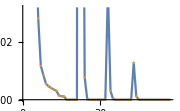

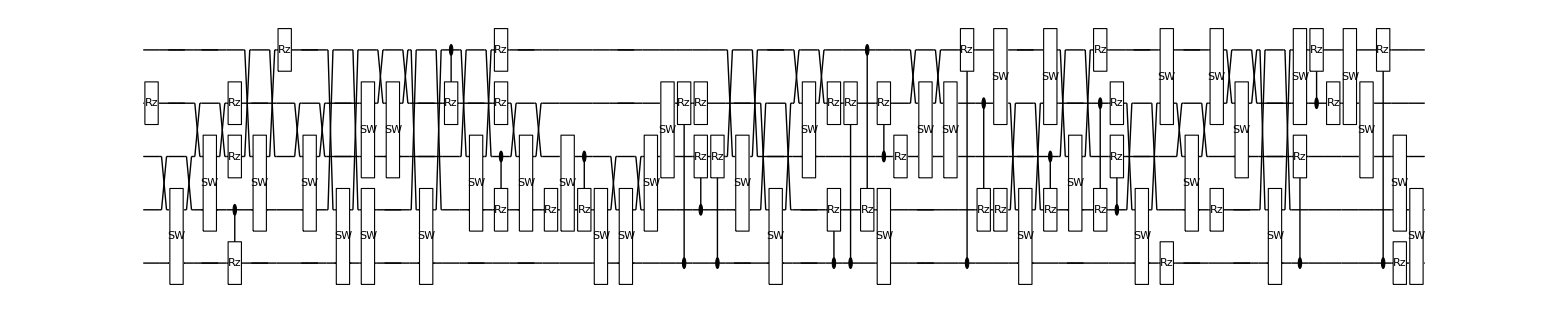

**** Compile @Sat 17 Dec 2022 05:37:51 τ=13.4; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 05:43:05 completed with ngates=36, cost=0.00008184579329717501, at eval=1562

Cycle 2@Sat 17 Dec 2022 05:47:30 completed with ngates=40, cost=6.995234643425441e-6, at eval=2895

Cycle 3@Sat 17 Dec 2022 05:53:53 completed with ngates=51, cost=8.29392383550065e-7, at eval=4279

Cycle 4@Sat 17 Dec 2022 06:02:57 completed with ngates=62, cost=1.300671411685883e-7, at eval=5811

Cycle 5@Sat 17 Dec 2022 06:06:25 adjust hyperparams, slowdown:True

Cycle 6@Sat 17 Dec 2022 06:29:56 completed with ngates=91, cost=1.0213820345050806e-8, at eval=8309

Cycle 7@Sat 17 Dec 2022 06:41:25 adjust hyperparams, slowdown:True

Cycle 8@Sat 17 Dec 2022 07:05:05 adjust hyperparams, slowdown:True

Cycle 9@Sat 17 Dec 2022 07:11:20 adjust hyperparams, slowdown:False

Cycle 10@Sat 17 Dec 2022 07:17:58 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.02138×10^-8

τ=13.6; δ=0.2; cost=1.02138×10^-8; ngates=91; runtime=108.123 min

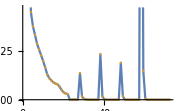

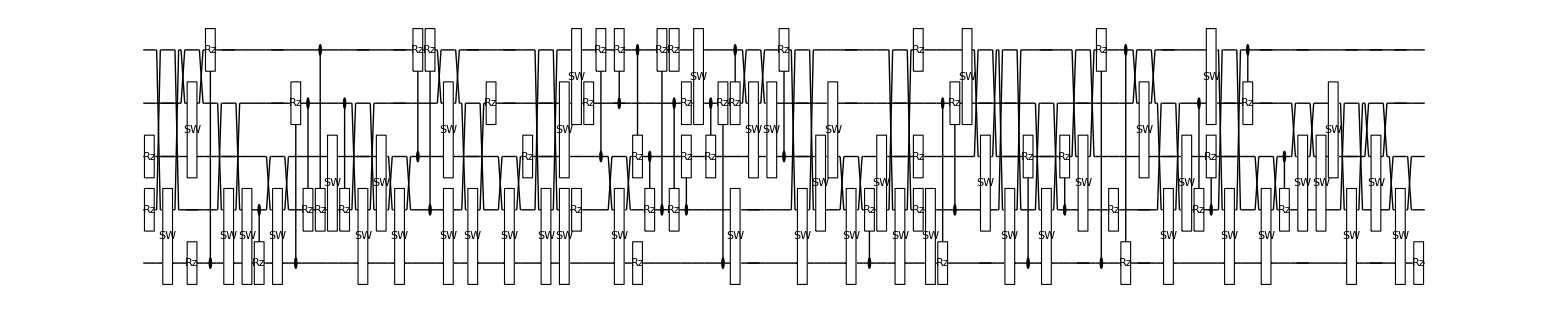

**** Compile @Sat 17 Dec 2022 07:26:04 τ=13.6; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 07:31:28 completed with ngates=35, cost=0.00009682778094477484, at eval=1569

Cycle 2@Sat 17 Dec 2022 07:35:33 completed with ngates=39, cost=0.000025869603053507717, at eval=2883

Cycle 3@Sat 17 Dec 2022 07:40:58 completed with ngates=45, cost=9.988636435753762e-7, at eval=4236

Cycle 4@Sat 17 Dec 2022 07:43:26 adjust hyperparams, slowdown:True

Cycle 5@Sat 17 Dec 2022 07:56:54 completed with ngates=43, cost=1.2943593652448016e-7, at eval=7135

Cycle 6@Sat 17 Dec 2022 08:09:14 completed with ngates=66, cost=1.2412097238900799e-8, at eval=8854

Cycle 7@Sat 17 Dec 2022 08:16:27 adjust hyperparams, slowdown:True

Cycle 8@Sat 17 Dec 2022 08:33:13 adjust hyperparams, slowdown:True

Cycle 9@Sat 17 Dec 2022 08:37:08 adjust hyperparams, slowdown:False

Cycle 10@Sat 17 Dec 2022 08:41:10 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.24121×10^-8

τ=13.8; δ=0.2; cost=1.24121×10^-8; ngates=66; runtime=78.6105 min

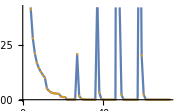

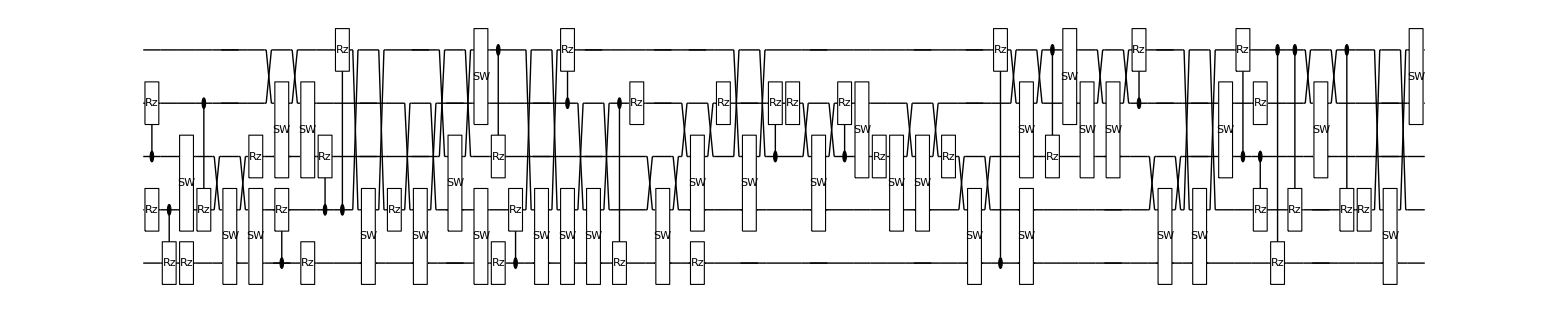

**** Compile @Sat 17 Dec 2022 08:44:41 τ=13.8; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 08:50:58 completed with ngates=45, cost=0.000021479614263242297, at eval=1724

Cycle 2@Sat 17 Dec 2022 08:53:23 adjust hyperparams, slowdown:True

Cycle 3@Sat 17 Dec 2022 08:58:17 adjust hyperparams, slowdown:True

Cycle 4@Sat 17 Dec 2022 09:15:57 completed with ngates=45, cost=2.292669086467747e-6, at eval=4650

Cycle 5@Sat 17 Dec 2022 09:28:56 adjust hyperparams, slowdown:True

Cycle 6@Sat 17 Dec 2022 09:36:03 completed with ngates=49, cost=3.134511716851307e-7, at eval=6884

Cycle 7@Sat 17 Dec 2022 09:44:58 completed with ngates=59, cost=1.7292676735003454e-7, at eval=8366

Cycle 8@Sat 17 Dec 2022 09:48:34 adjust hyperparams, slowdown:False

Cycle 9@Sat 17 Dec 2022 09:59:48 completed with ngates=63, cost=4.221753568955933e-8, at eval=10414

Cycle 10@Sat 17 Dec 2022 10:13:40 completed with ngates=73, cost=1.4231463119074306e-8, at eval=12106

Cycle 11@Sat 17 Dec 2022 10:18:47 adjust hyperparams, slowdown:False

Cycle 12@Sat 17 Dec 2022 10:24:15 adjust hyperparams, slowdown:False

Cycle 13@Sat 17 Dec 2022 10:29:43 adjust hyperparams, slowdown:False

Cycle 14@Sat 17 Dec 2022 10:35:35 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.42315×10^-8

τ=14.; δ=0.2; cost=1.42315×10^-8; ngates=73; runtime=115.802 min

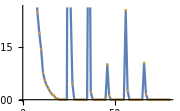

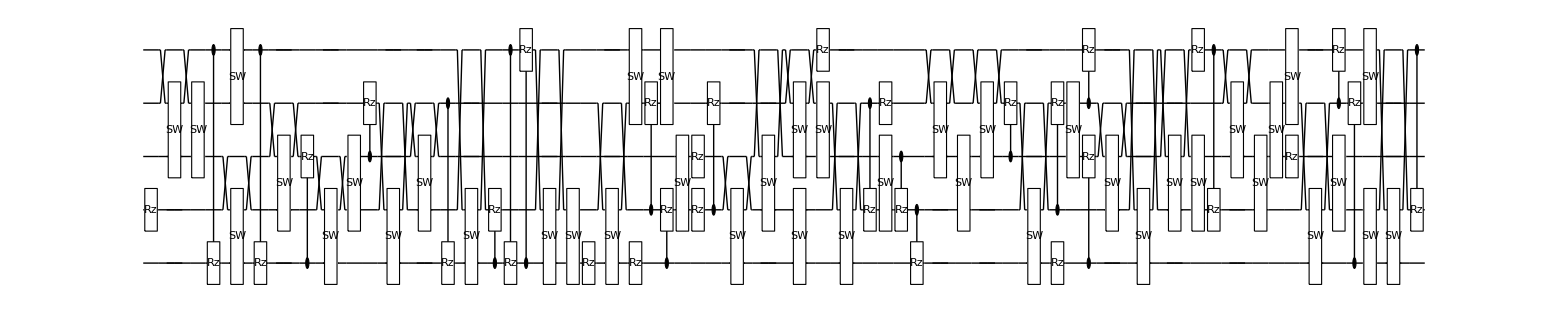

**** Compile @Sat 17 Dec 2022 10:40:29 τ=14.; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 10:46:24 completed with ngates=41, cost=1.6809168912335082e-6, at eval=1574

Cycle 2@Sat 17 Dec 2022 10:48:42 adjust hyperparams, slowdown:True

Cycle 3@Sat 17 Dec 2022 10:53:22 adjust hyperparams, slowdown:True

Cycle 4@Sat 17 Dec 2022 11:05:15 adjust hyperparams, slowdown:True

Cycle 5@Sat 17 Dec 2022 11:07:32 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.68092×10^-6

τ=14.2; δ=0.2; cost=1.68092×10^-6; ngates=41; runtime=28.0887 min

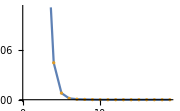

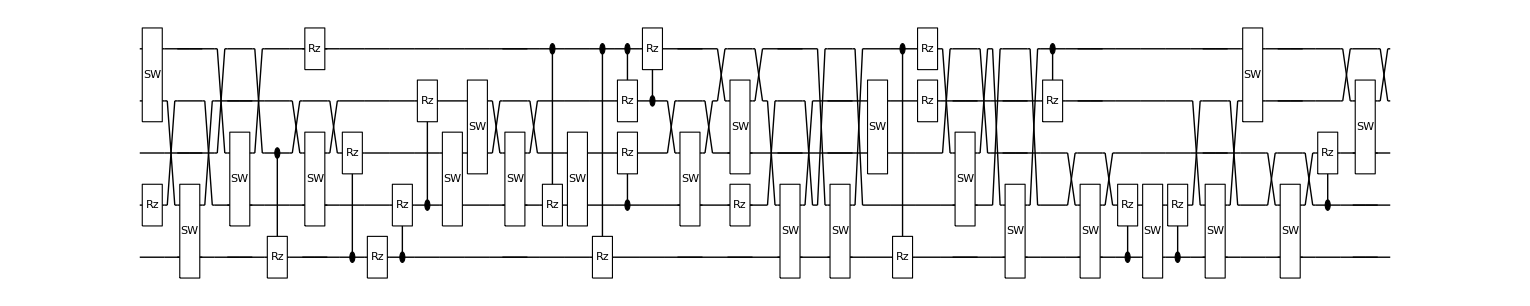

**** Compile @Sat 17 Dec 2022 11:08:35 τ=14.2; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 11:15:30 completed with ngates=47, cost=1.1327874647193426e-6, at eval=1719

Cycle 2@Sat 17 Dec 2022 11:18:08 adjust hyperparams, slowdown:True

Cycle 3@Sat 17 Dec 2022 11:32:41 completed with ngates=58, cost=1.1038136282781608e-7, at eval=4397

Cycle 4@Sat 17 Dec 2022 11:38:56 adjust hyperparams, slowdown:True

Cycle 5@Sat 17 Dec 2022 11:53:45 adjust hyperparams, slowdown:True

Cycle 6@Sat 17 Dec 2022 11:57:01 adjust hyperparams, slowdown:False

Cycle 7@Sat 17 Dec 2022 12:07:26 completed with ngates=67, cost=5.656858270697285e-8, at eval=7854

Cycle 8@Sat 17 Dec 2022 12:21:19 completed with ngates=79, cost=5.231863853261132e-8, at eval=9639

Cycle 9@Sat 17 Dec 2022 12:26:15 adjust hyperparams, slowdown:False

Cycle 10@Sat 17 Dec 2022 12:43:27 completed with ngates=84, cost=9.643176479556814e-9, at eval=12028

Cycle 11@Sat 17 Dec 2022 12:49:04 adjust hyperparams, slowdown:False

Cycle 12@Sat 17 Dec 2022 12:54:56 adjust hyperparams, slowdown:False

Cycle 13@Sat 17 Dec 2022 13:01:06 adjust hyperparams, slowdown:False

Cycle 14@Sat 17 Dec 2022 13:07:40 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=9.64318×10^-9

τ=14.4; δ=0.2; cost=9.64318×10^-9; ngates=84; runtime=125.212 min

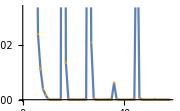

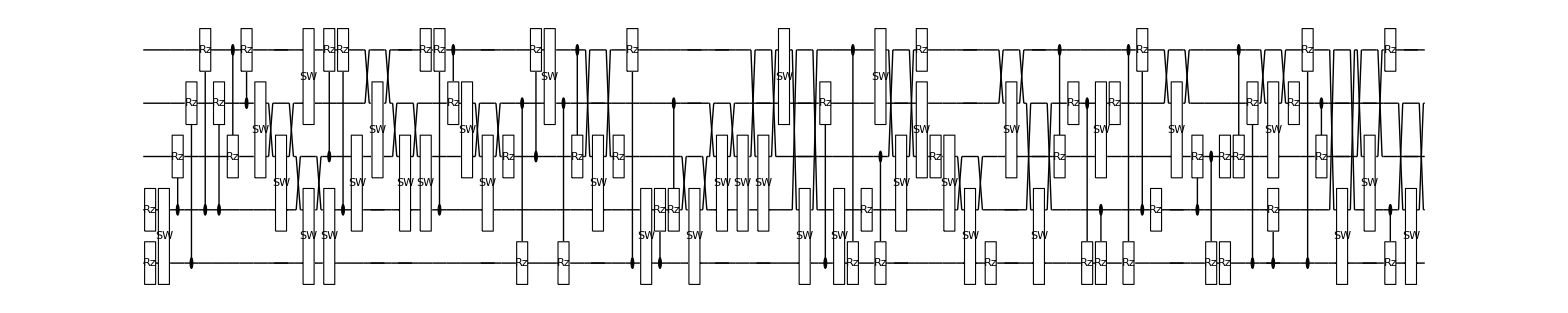

**** Compile @Sat 17 Dec 2022 13:13:48 τ=14.4; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 13:19:39 completed with ngates=38, cost=1.0204625868759365e-6, at eval=1682

Cycle 2@Sat 17 Dec 2022 13:21:37 adjust hyperparams, slowdown:True

Cycle 3@Sat 17 Dec 2022 13:25:49 adjust hyperparams, slowdown:True

Cycle 4@Sat 17 Dec 2022 13:36:53 adjust hyperparams, slowdown:True

Cycle 5@Sat 17 Dec 2022 13:38:55 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.02046×10^-6

τ=14.6; δ=0.2; cost=1.02046×10^-6; ngates=38; runtime=26.099 min

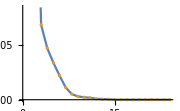

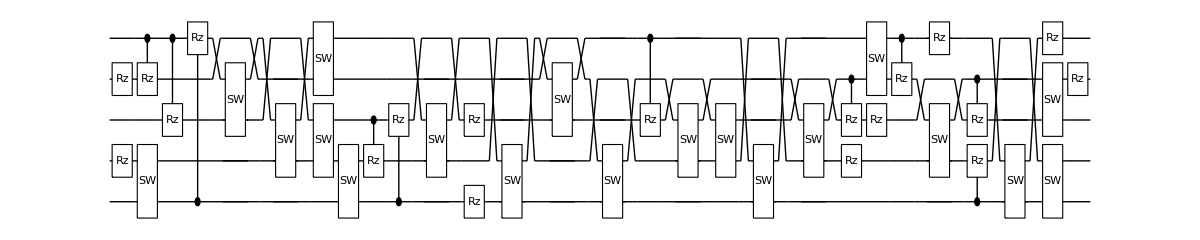

**** Compile @Sat 17 Dec 2022 13:39:55 τ=14.6; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 13:45:43 completed with ngates=40, cost=6.650701310340068e-6, at eval=1576

Cycle 2@Sat 17 Dec 2022 13:48:03 adjust hyperparams, slowdown:True

Cycle 3@Sat 17 Dec 2022 13:52:43 adjust hyperparams, slowdown:True

Cycle 4@Sat 17 Dec 2022 14:04:21 adjust hyperparams, slowdown:True

Cycle 5@Sat 17 Dec 2022 14:06:39 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=6.6507×10^-6

τ=14.8; δ=0.2; cost=5.13189×10^-6; ngates=40; runtime=27.8635 min

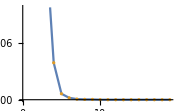

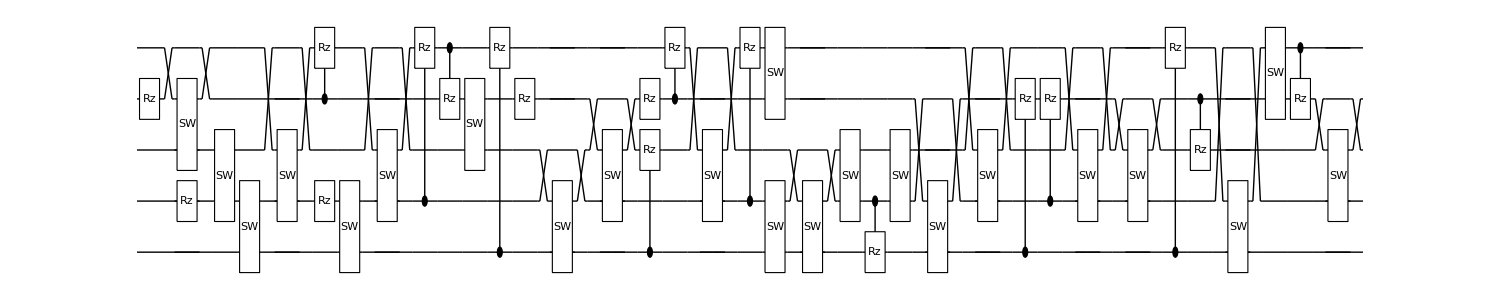

**** Compile @Sat 17 Dec 2022 14:07:47 τ=14.8; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 14:13:57 completed with ngates=41, cost=4.729487230958895e-6, at eval=1757

Cycle 2@Sat 17 Dec 2022 14:16:00 adjust hyperparams, slowdown:True

Cycle 3@Sat 17 Dec 2022 14:20:09 adjust hyperparams, slowdown:True

Cycle 4@Sat 17 Dec 2022 14:39:29 completed with ngates=47, cost=7.168473613594628e-7, at eval=5130

Cycle 5@Sat 17 Dec 2022 14:52:33 adjust hyperparams, slowdown:True

Cycle 6@Sat 17 Dec 2022 14:55:08 adjust hyperparams, slowdown:False

Cycle 7@Sat 17 Dec 2022 15:02:08 completed with ngates=53, cost=2.0319069760077468e-7, at eval=7805

Cycle 8@Sat 17 Dec 2022 15:05:16 adjust hyperparams, slowdown:False

Cycle 9@Sat 17 Dec 2022 15:08:36 adjust hyperparams, slowdown:False

Cycle 10@Sat 17 Dec 2022 15:11:54 adjust hyperparams, slowdown:False

Cycle 11@Sat 17 Dec 2022 15:15:21 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=2.03191×10^-7

τ=15.; δ=0.2; cost=2.03191×10^-7; ngates=53; runtime=69.9019 min

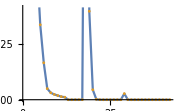

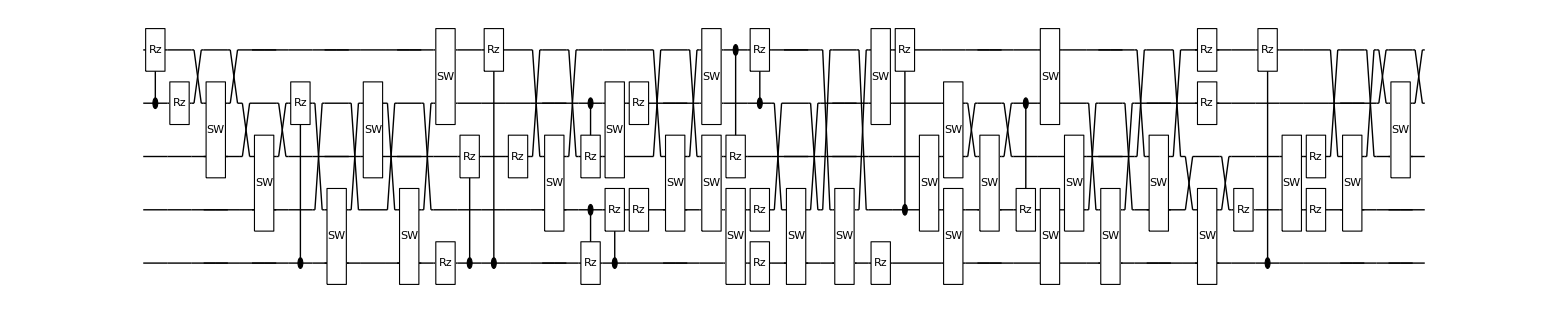

**** Compile @Sat 17 Dec 2022 15:17:43 τ=15.; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 15:23:24 completed with ngates=32, cost=0.00001823986195315097, at eval=1700

Cycle 2@Sat 17 Dec 2022 15:29:22 completed with ngates=40, cost=2.4141121298670853e-6, at eval=3495

Cycle 3@Sat 17 Dec 2022 15:31:39 adjust hyperparams, slowdown:True

Cycle 4@Sat 17 Dec 2022 15:36:34 adjust hyperparams, slowdown:True

Cycle 5@Sat 17 Dec 2022 15:48:24 adjust hyperparams, slowdown:True

Cycle 6@Sat 17 Dec 2022 15:50:46 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=2.41411×10^-6

τ=15.2; δ=0.2; cost=2.41411×10^-6; ngates=40; runtime=34.399 min

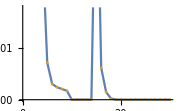

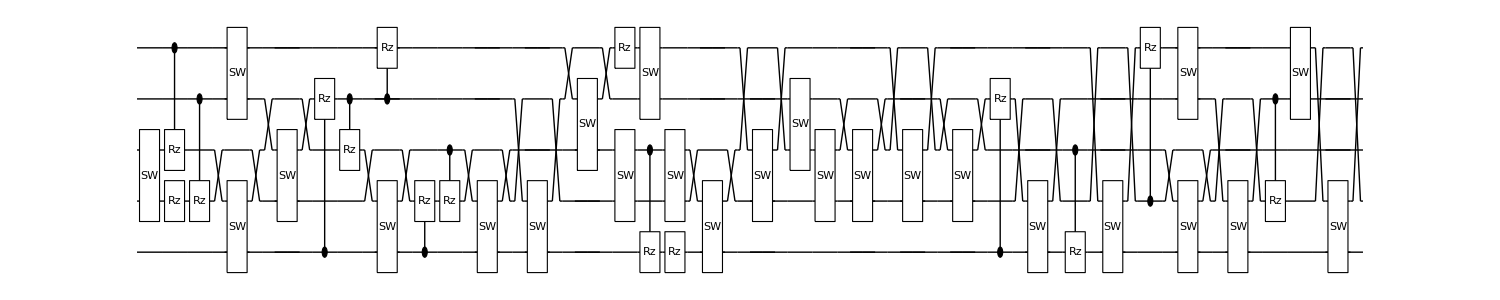

**** Compile @Sat 17 Dec 2022 15:52:08 τ=15.2; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 15:58:00 completed with ngates=36, cost=0.00008993565014647764, at eval=1864

Cycle 2@Sat 17 Dec 2022 15:59:47 adjust hyperparams, slowdown:True

Cycle 3@Sat 17 Dec 2022 16:06:23 completed with ngates=38, cost=4.566663270089144e-6, at eval=3766

Cycle 4@Sat 17 Dec 2022 16:14:38 completed with ngates=44, cost=2.2556004308782462e-7, at eval=5356

Cycle 5@Sat 17 Dec 2022 16:19:37 adjust hyperparams, slowdown:True

Cycle 6@Sat 17 Dec 2022 16:32:22 adjust hyperparams, slowdown:True

Cycle 7@Sat 17 Dec 2022 16:34:44 adjust hyperparams, slowdown:False

Cycle 8@Sat 17 Dec 2022 16:37:15 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=2.2556×10^-7

τ=15.4; δ=0.2; cost=2.2556×10^-7; ngates=44; runtime=46.6681 min

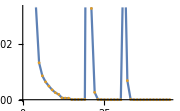

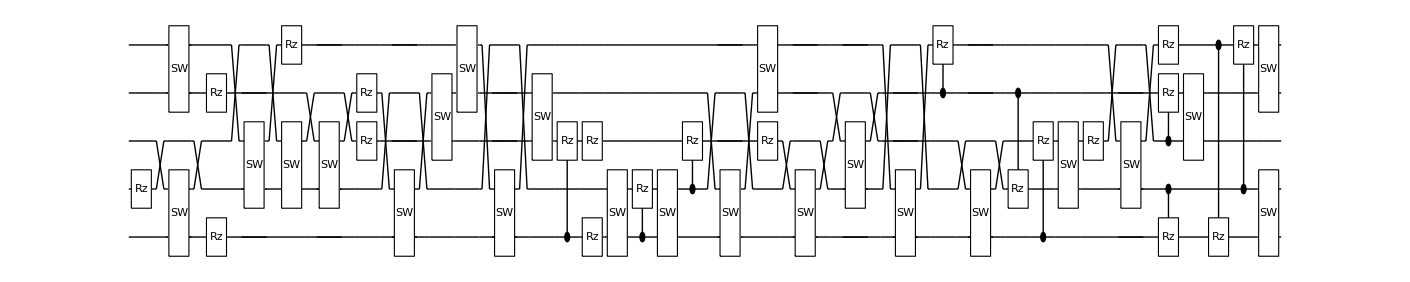

**** Compile @Sat 17 Dec 2022 16:38:48 τ=15.4; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 16:44:09 completed with ngates=38, cost=2.7959305426428216e-8, at eval=1522

Cycle 2@Sat 17 Dec 2022 16:46:07 adjust hyperparams, slowdown:True

Cycle 3@Sat 17 Dec 2022 16:50:13 adjust hyperparams, slowdown:True

Cycle 4@Sat 17 Dec 2022 17:01:23 adjust hyperparams, slowdown:True

Cycle 5@Sat 17 Dec 2022 17:03:22 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=2.79593×10^-8

τ=15.6; δ=0.2; cost=2.79593×10^-8; ngates=38; runtime=25.3137 min

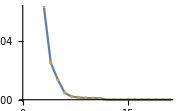

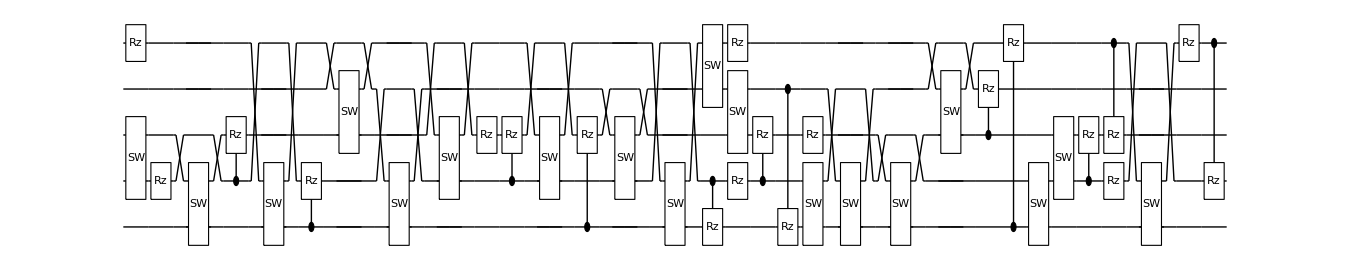

**** Compile @Sat 17 Dec 2022 17:04:10 τ=15.6; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 17:09:38 completed with ngates=36, cost=5.361322820141012e-6, at eval=1621

Cycle 2@Sat 17 Dec 2022 17:11:34 adjust hyperparams, slowdown:True

Cycle 3@Sat 17 Dec 2022 17:21:40 completed with ngates=49, cost=6.142825057509071e-7, at eval=4062

Cycle 4@Sat 17 Dec 2022 17:27:04 adjust hyperparams, slowdown:True

Cycle 5@Sat 17 Dec 2022 17:40:35 adjust hyperparams, slowdown:True

Cycle 6@Sat 17 Dec 2022 17:43:23 adjust hyperparams, slowdown:False

Cycle 7@Sat 17 Dec 2022 17:46:09 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=6.14283×10^-7

τ=15.8; δ=0.2; cost=6.14283×10^-7; ngates=49; runtime=43.7023 min

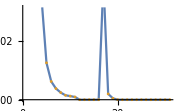

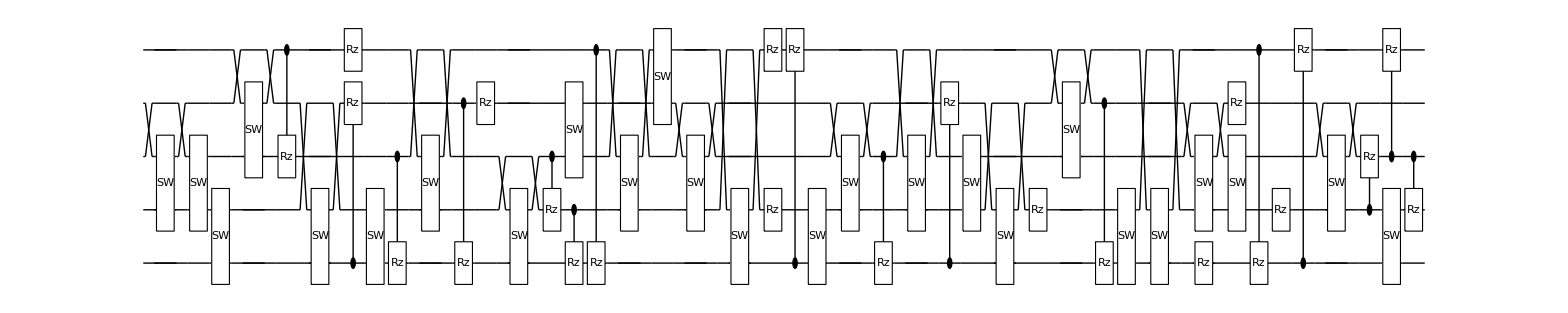

**** Compile @Sat 17 Dec 2022 17:47:54 τ=15.8; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 17:55:33 completed with ngates=52, cost=1.8355048305718213e-6, at eval=1844

Cycle 2@Sat 17 Dec 2022 17:58:26 adjust hyperparams, slowdown:True

Cycle 3@Sat 17 Dec 2022 18:04:17 adjust hyperparams, slowdown:True

Cycle 4@Sat 17 Dec 2022 18:17:46 adjust hyperparams, slowdown:True

Cycle 5@Sat 17 Dec 2022 18:20:56 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.8355×10^-6

τ=16.; δ=0.2; cost=1.66421×10^-6; ngates=52; runtime=35.058 min

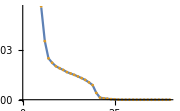

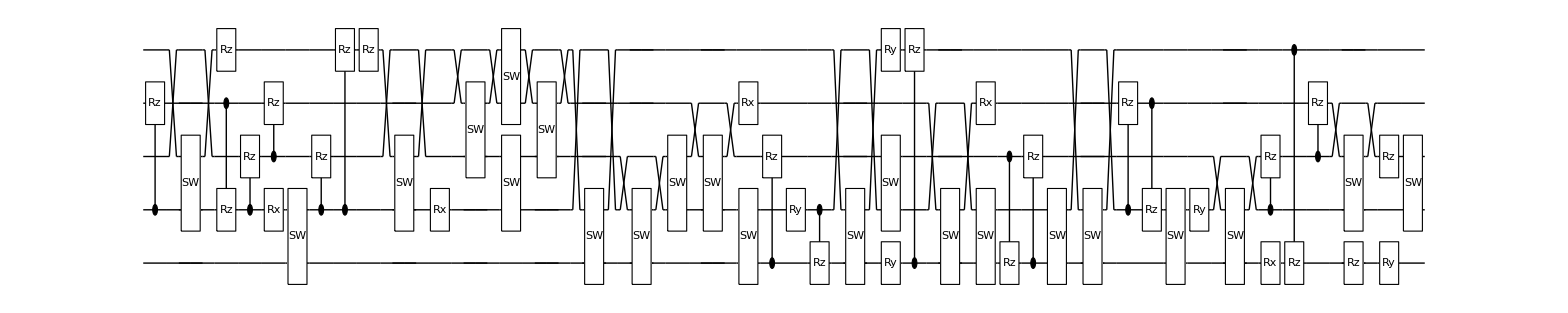

**** Compile @Sat 17 Dec 2022 18:23:00 τ=16.; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 18:28:37 completed with ngates=39, cost=0.000014753507926013043, at eval=1698

Cycle 2@Sat 17 Dec 2022 18:34:59 completed with ngates=45, cost=1.2225861435455343e-6, at eval=3620

Cycle 3@Sat 17 Dec 2022 18:37:22 adjust hyperparams, slowdown:True

Cycle 4@Sat 17 Dec 2022 18:42:07 adjust hyperparams, slowdown:True

Cycle 5@Sat 17 Dec 2022 18:54:16 adjust hyperparams, slowdown:True

Cycle 6@Sat 17 Dec 2022 18:56:38 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.22259×10^-6

τ=16.2; δ=0.2; cost=1.22259×10^-6; ngates=45; runtime=35.1239 min

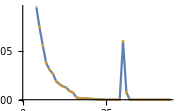

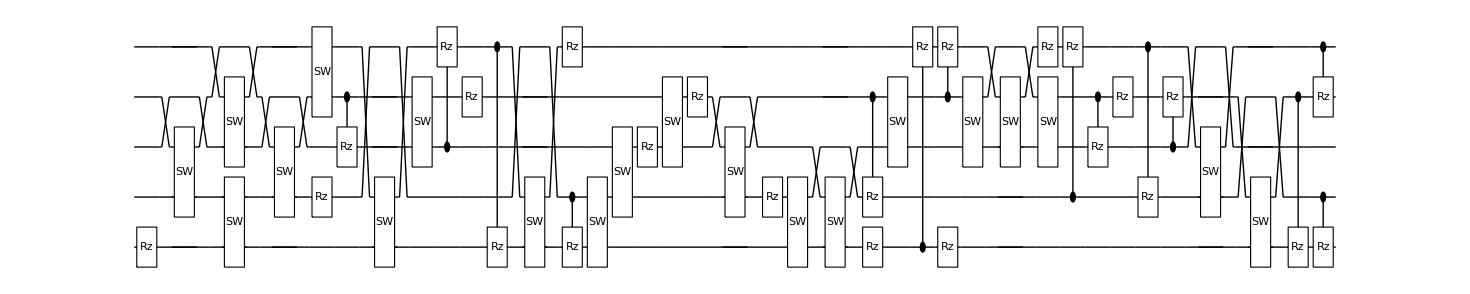

**** Compile @Sat 17 Dec 2022 18:58:07 τ=16.2; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 19:04:19 completed with ngates=41, cost=2.0462227561246493e-6, at eval=1698

Cycle 2@Sat 17 Dec 2022 19:09:33 completed with ngates=46, cost=1.5756522486753965e-7, at eval=3062

Cycle 3@Sat 17 Dec 2022 19:17:01 completed with ngates=59, cost=4.111135498696683e-8, at eval=4512

Cycle 4@Sat 17 Dec 2022 19:20:09 adjust hyperparams, slowdown:True

Cycle 5@Sat 17 Dec 2022 19:26:32 adjust hyperparams, slowdown:True

Cycle 6@Sat 17 Dec 2022 19:41:30 adjust hyperparams, slowdown:True

Cycle 7@Sat 17 Dec 2022 19:44:38 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=4.11114×10^-8

τ=16.4; δ=0.2; cost=4.11114×10^-8; ngates=59; runtime=49.1139 min

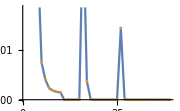

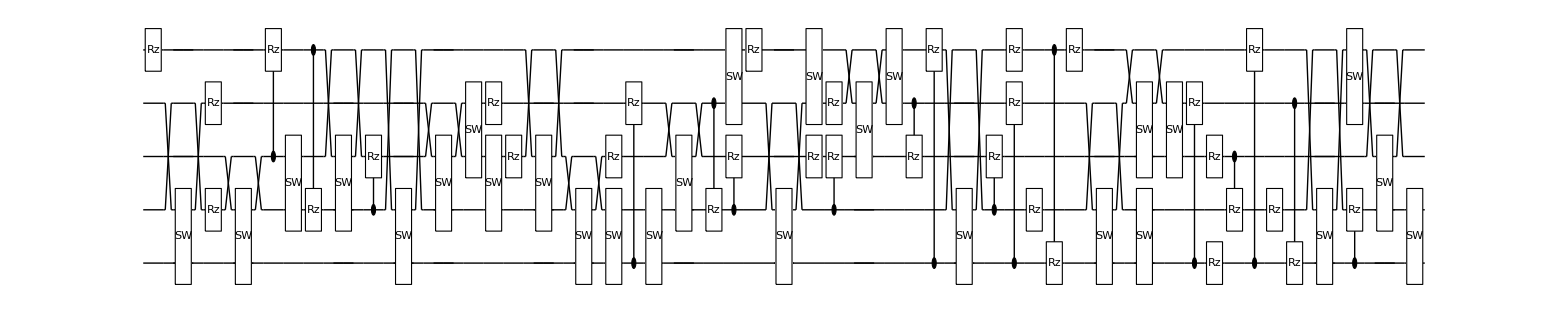

**** Compile @Sat 17 Dec 2022 19:47:14 τ=16.4; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 19:53:36 completed with ngates=40, cost=0.000019623848359628937, at eval=1843

Cycle 2@Sat 17 Dec 2022 19:58:47 completed with ngates=40, cost=2.2278125171304453e-6, at eval=3268

Cycle 3@Sat 17 Dec 2022 20:07:05 completed with ngates=49, cost=7.519887645912604e-8, at eval=5177

Cycle 4@Sat 17 Dec 2022 20:09:46 adjust hyperparams, slowdown:True

Cycle 5@Sat 17 Dec 2022 20:26:23 completed with ngates=81, cost=8.216466618193863e-9, at eval=7531

Cycle 6@Sat 17 Dec 2022 20:35:12 adjust hyperparams, slowdown:True

Cycle 7@Sat 17 Dec 2022 20:54:59 adjust hyperparams, slowdown:True

Cycle 8@Sat 17 Dec 2022 20:59:50 adjust hyperparams, slowdown:False

Cycle 9@Sat 17 Dec 2022 21:04:56 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=8.21647×10^-9

τ=16.6; δ=0.2; cost=8.21647×10^-9; ngates=81; runtime=83.3899 min

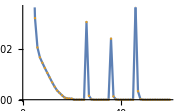

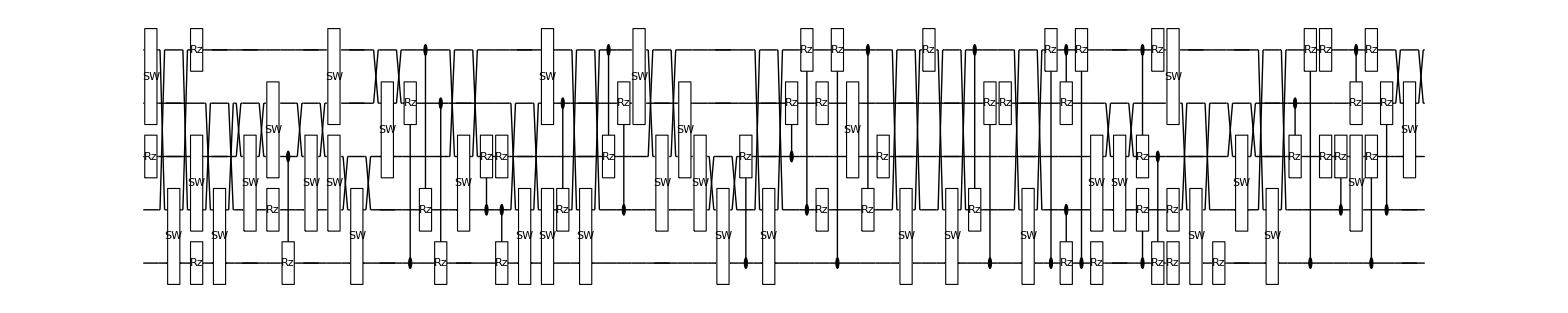

**** Compile @Sat 17 Dec 2022 21:10:38 τ=16.6; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 21:17:50 completed with ngates=36, cost=4.574975296378625e-7, at eval=2129

Cycle 2@Sat 17 Dec 2022 21:19:47 adjust hyperparams, slowdown:True

Cycle 3@Sat 17 Dec 2022 21:24:06 adjust hyperparams, slowdown:True

Cycle 4@Sat 17 Dec 2022 21:35:06 adjust hyperparams, slowdown:True

Cycle 5@Sat 17 Dec 2022 21:37:09 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=4.57498×10^-7

τ=16.8; δ=0.2; cost=4.57498×10^-7; ngates=36; runtime=27.493 min

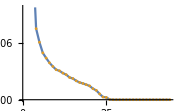

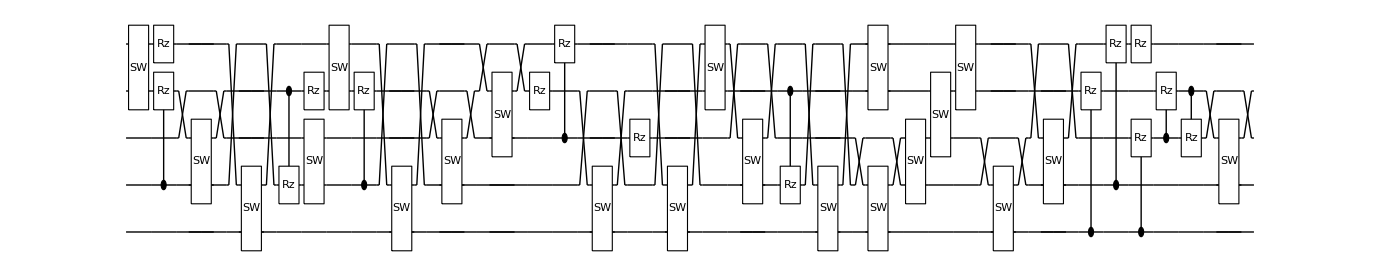

**** Compile @Sat 17 Dec 2022 21:38:10 τ=16.8; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 21:44:59 completed with ngates=46, cost=2.0836040135474576e-6, at eval=1662

Cycle 2@Sat 17 Dec 2022 21:53:49 completed with ngates=49, cost=3.987058218024586e-7, at eval=3574

Cycle 3@Sat 17 Dec 2022 22:02:33 completed with ngates=61, cost=1.6245697520567148e-7, at eval=5077

Cycle 4@Sat 17 Dec 2022 22:16:28 completed with ngates=76, cost=1.7312368538746625e-8, at eval=6759

Cycle 5@Sat 17 Dec 2022 22:37:17 completed with ngates=90, cost=1.3773413964912606e-8, at eval=8654

Cycle 6@Sat 17 Dec 2022 22:43:15 adjust hyperparams, slowdown:True

Cycle 7@Sat 17 Dec 2022 22:54:20 adjust hyperparams, slowdown:True

Cycle 8@Sat 17 Dec 2022 23:17:16 adjust hyperparams, slowdown:True

Cycle 9@Sat 17 Dec 2022 23:23:38 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.37734×10^-8

τ=17.; δ=0.2; cost=1.37734×10^-8; ngates=90; runtime=113.306 min

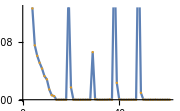

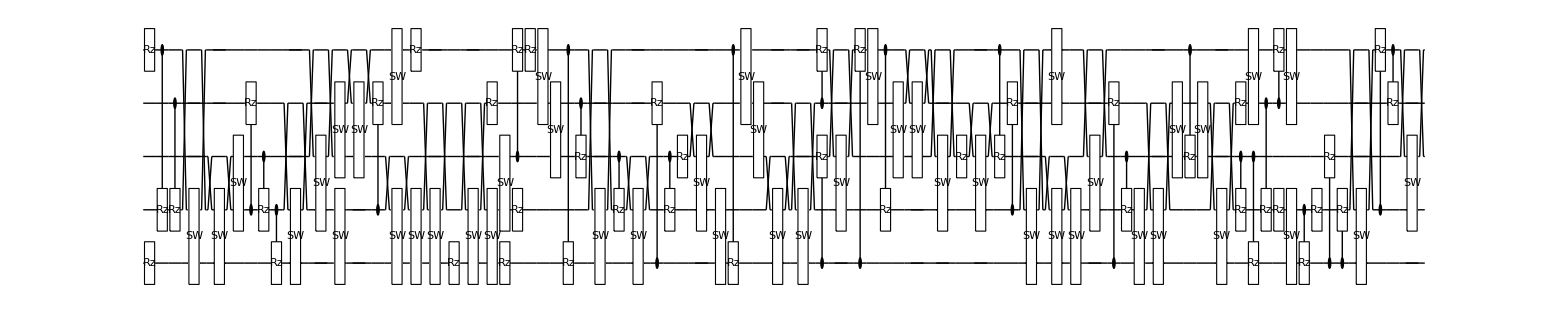

**** Compile @Sat 17 Dec 2022 23:31:30 τ=17.; δ0.2 ****

Cycle 1@Sat 17 Dec 2022 23:39:46 completed with ngates=38, cost=8.733264330595958e-7, at eval=2613

Cycle 2@Sat 17 Dec 2022 23:41:49 adjust hyperparams, slowdown:True

Cycle 3@Sat 17 Dec 2022 23:46:10 adjust hyperparams, slowdown:True

Cycle 4@Sat 17 Dec 2022 23:57:34 adjust hyperparams, slowdown:True

Cycle 5@Sat 17 Dec 2022 23:59:45 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=8.73326×10^-7

τ=17.2; δ=0.2; cost=8.73326×10^-7; ngates=38; runtime=29.3626 min

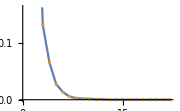

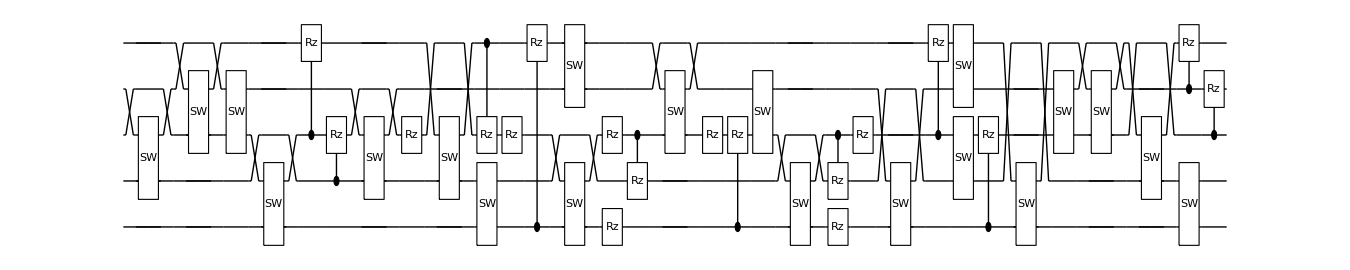

**** Compile @Sun 18 Dec 2022 00:00:52 τ=17.2; δ0.2 ****

Cycle 1@Sun 18 Dec 2022 00:07:28 completed with ngates=42, cost=3.8325192518451345e-6, at eval=1612

Cycle 2@Sun 18 Dec 2022 00:15:23 completed with ngates=43, cost=2.0591907634592843e-7, at eval=3366

Cycle 3@Sun 18 Dec 2022 00:18:00 adjust hyperparams, slowdown:True

Cycle 4@Sun 18 Dec 2022 00:23:18 adjust hyperparams, slowdown:True

Cycle 5@Sun 18 Dec 2022 01:00:07 completed with ngates=73, cost=4.112865215066819e-8, at eval=7757

Cycle 6@Sun 18 Dec 2022 01:19:52 adjust hyperparams, slowdown:True

Cycle 7@Sun 18 Dec 2022 01:24:42 adjust hyperparams, slowdown:False

Cycle 8@Sun 18 Dec 2022 01:42:05 completed with ngates=80, cost=1.2802219062635345e-8, at eval=10770

Cycle 9@Sun 18 Dec 2022 01:48:02 adjust hyperparams, slowdown:False

Cycle 10@Sun 18 Dec 2022 02:09:32 completed with ngates=88, cost=5.129852320706618e-9, at eval=13230

Cycle 11@Sun 18 Dec 2022 02:35:45 completed with ngates=96, cost=3.4164584494789096e-9, at eval=15320

Cycle 12@Sun 18 Dec 2022 02:43:32 adjust hyperparams, slowdown:False

Cycle 13@Sun 18 Dec 2022 02:51:43 adjust hyperparams, slowdown:False

@cycle14, pathetic result.

Cycle 14@Sun 18 Dec 2022 03:00:18 adjust hyperparams, slowdown:False

Cycle 15@Sun 18 Dec 2022 03:09:36 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=3.41646×10^-9

τ=17.4; δ=0.2; cost=3.41646×10^-9; ngates=96; runtime=198.417 min

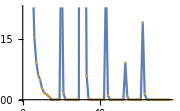

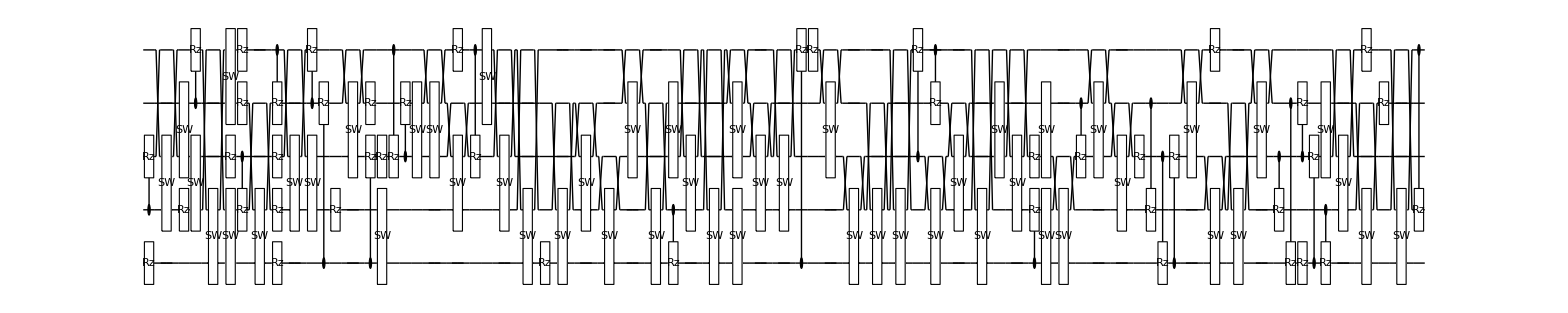

**** Compile @Sun 18 Dec 2022 03:19:24 τ=17.4; δ0.2 ****

Cycle 1@Sun 18 Dec 2022 03:26:15 completed with ngates=49, cost=1.9530998183192594e-6, at eval=1728

Cycle 2@Sun 18 Dec 2022 03:28:54 adjust hyperparams, slowdown:True

Cycle 3@Sun 18 Dec 2022 03:34:23 adjust hyperparams, slowdown:True

Cycle 4@Sun 18 Dec 2022 03:47:10 adjust hyperparams, slowdown:True

Cycle 5@Sun 18 Dec 2022 03:49:48 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.9531×10^-6

τ=17.6; δ=0.2; cost=1.9531×10^-6; ngates=49; runtime=32.0218 min

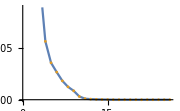

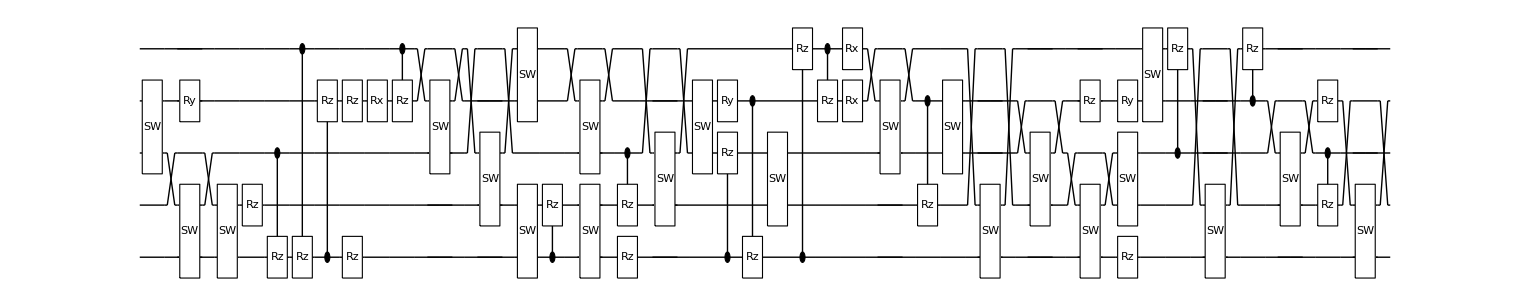

**** Compile @Sun 18 Dec 2022 03:51:28 τ=17.6; δ0.2 ****

Cycle 1@Sun 18 Dec 2022 03:56:51 completed with ngates=38, cost=9.565381399734285e-6, at eval=1651

Cycle 2@Sun 18 Dec 2022 03:58:42 adjust hyperparams, slowdown:True

Cycle 3@Sun 18 Dec 2022 04:10:38 completed with ngates=57, cost=4.57128017217201e-7, at eval=4361

Cycle 4@Sun 18 Dec 2022 04:33:55 completed with ngates=79, cost=4.7822598325808485e-8, at eval=6958

Cycle 5@Sun 18 Dec 2022 04:43:00 adjust hyperparams, slowdown:True

Cycle 6@Sun 18 Dec 2022 05:03:11 adjust hyperparams, slowdown:True

Cycle 7@Sun 18 Dec 2022 05:08:03 adjust hyperparams, slowdown:False

Cycle 8@Sun 18 Dec 2022 05:13:17 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=4.78226×10^-8

τ=17.8; δ=0.2; cost=4.78226×10^-8; ngates=79; runtime=87.4113 min

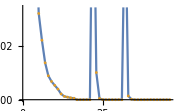

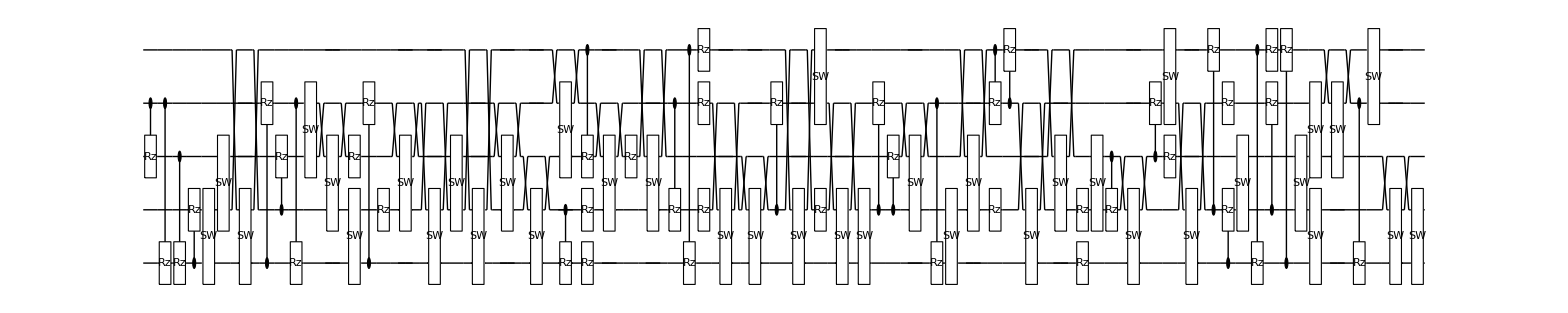

**** Compile @Sun 18 Dec 2022 05:18:56 τ=17.8; δ0.2 ****

Cycle 1@Sun 18 Dec 2022 05:24:48 completed with ngates=41, cost=6.855335755950875e-6, at eval=1684

Cycle 2@Sun 18 Dec 2022 05:30:01 completed with ngates=43, cost=5.669700766652852e-7, at eval=3025

Cycle 3@Sun 18 Dec 2022 05:37:07 completed with ngates=55, cost=2.8924902095717187e-7, at eval=4433

Cycle 4@Sun 18 Dec 2022 05:40:13 adjust hyperparams, slowdown:True

Cycle 5@Sun 18 Dec 2022 05:46:33 adjust hyperparams, slowdown:True

Cycle 6@Sun 18 Dec 2022 06:01:16 adjust hyperparams, slowdown:True

Cycle 7@Sun 18 Dec 2022 06:12:10 completed with ngates=68, cost=9.388751842642762e-8, at eval=7791

Cycle 8@Sun 18 Dec 2022 06:27:38 completed with ngates=80, cost=2.8167825849578776e-8, at eval=9542

Cycle 9@Sun 18 Dec 2022 06:32:49 adjust hyperparams, slowdown:False

Cycle 10@Sun 18 Dec 2022 06:52:44 completed with ngates=89, cost=1.562800822085819e-8, at eval=11902

Cycle 11@Sun 18 Dec 2022 06:58:54 adjust hyperparams, slowdown:False

Cycle 12@Sun 18 Dec 2022 07:05:35 adjust hyperparams, slowdown:False

Cycle 13@Sun 18 Dec 2022 07:12:28 adjust hyperparams, slowdown:False

Cycle 14@Sun 18 Dec 2022 07:37:10 completed with ngates=95, cost=1.0198260125271474e-8, at eval=15602

Cycle 15@Sun 18 Dec 2022 07:45:02 adjust hyperparams, slowdown:False

Cycle 16@Sun 18 Dec 2022 07:53:30 adjust hyperparams, slowdown:False

Cycle 17@Sun 18 Dec 2022 08:22:02 completed with ngates=98, cost=7.087161968399869e-10, at eval=19098

τ=18.; δ=0.2; cost=7.08716×10^-10; ngates=98; runtime=192.884 min

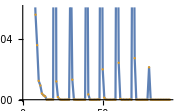

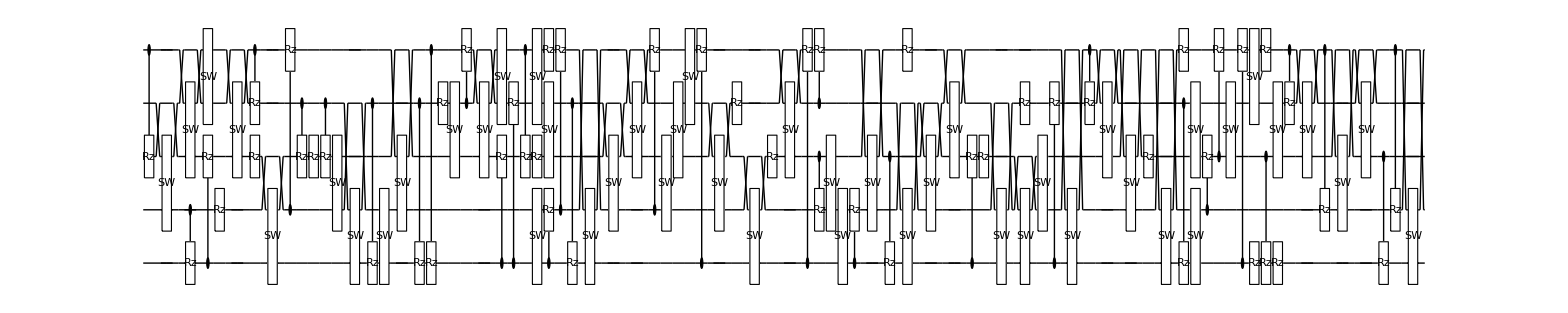

**** Compile @Sun 18 Dec 2022 08:31:49 τ=18.; δ0.2 ****

Cycle 1@Sun 18 Dec 2022 08:37:50 completed with ngates=42, cost=3.936794478187622e-7, at eval=1619

Cycle 2@Sun 18 Dec 2022 08:39:56 adjust hyperparams, slowdown:True

Cycle 3@Sun 18 Dec 2022 08:51:56 completed with ngates=66, cost=1.758132861517936e-8, at eval=3795

Cycle 4@Sun 18 Dec 2022 08:58:53 adjust hyperparams, slowdown:True

Cycle 5@Sun 18 Dec 2022 09:15:05 adjust hyperparams, slowdown:True

Cycle 6@Sun 18 Dec 2022 09:18:38 adjust hyperparams, slowdown:False

Cycle 7@Sun 18 Dec 2022 09:22:32 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.75813×10^-8

τ=18.2; δ=0.2; cost=1.75813×10^-8; ngates=66; runtime=54.1565 min

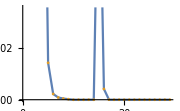

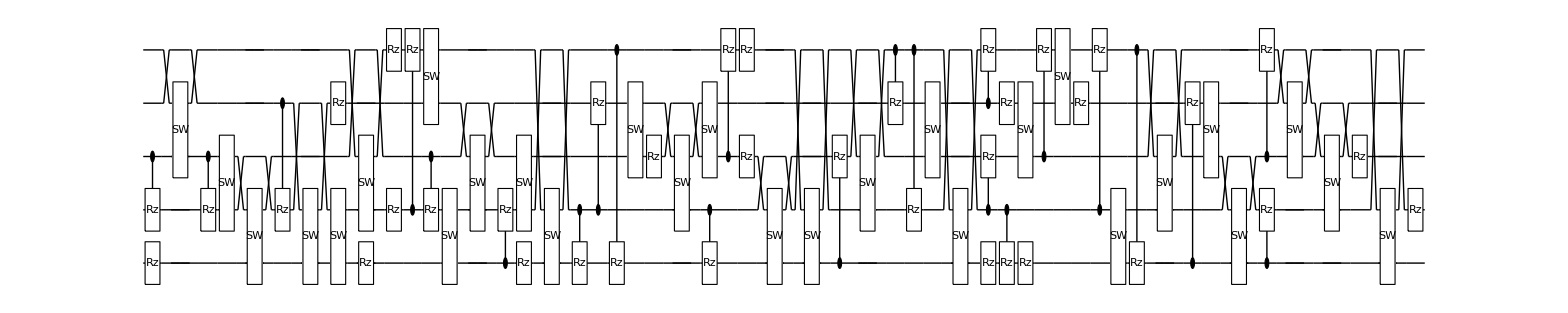

**** Compile @Sun 18 Dec 2022 09:26:01 τ=18.2; δ0.2 ****

Cycle 1@Sun 18 Dec 2022 09:32:36 completed with ngates=45, cost=1.279307078716485e-6, at eval=1677

Cycle 2@Sun 18 Dec 2022 09:40:30 completed with ngates=60, cost=3.827307616388609e-7, at eval=3172

Cycle 3@Sun 18 Dec 2022 09:43:45 adjust hyperparams, slowdown:True

Cycle 4@Sun 18 Dec 2022 09:50:16 adjust hyperparams, slowdown:True

Cycle 5@Sun 18 Dec 2022 10:05:45 adjust hyperparams, slowdown:True

Cycle 6@Sun 18 Dec 2022 10:16:28 completed with ngates=68, cost=8.380022198384296e-8, at eval=6576

Cycle 7@Sun 18 Dec 2022 10:30:21 completed with ngates=78, cost=1.1278652567447978e-8, at eval=8320

Cycle 8@Sun 18 Dec 2022 10:35:05 adjust hyperparams, slowdown:False

Cycle 9@Sun 18 Dec 2022 10:54:03 completed with ngates=89, cost=2.4812000232188325e-9, at eval=10706

Cycle 10@Sun 18 Dec 2022 10:59:51 adjust hyperparams, slowdown:False

Cycle 11@Sun 18 Dec 2022 11:06:01 adjust hyperparams, slowdown:False

Cycle 12@Sun 18 Dec 2022 11:12:28 adjust hyperparams, slowdown:False

Cycle 13@Sun 18 Dec 2022 11:19:13 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=2.4812×10^-9

τ=18.4; δ=0.2; cost=2.4812×10^-9; ngates=89; runtime=120.327 min

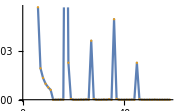

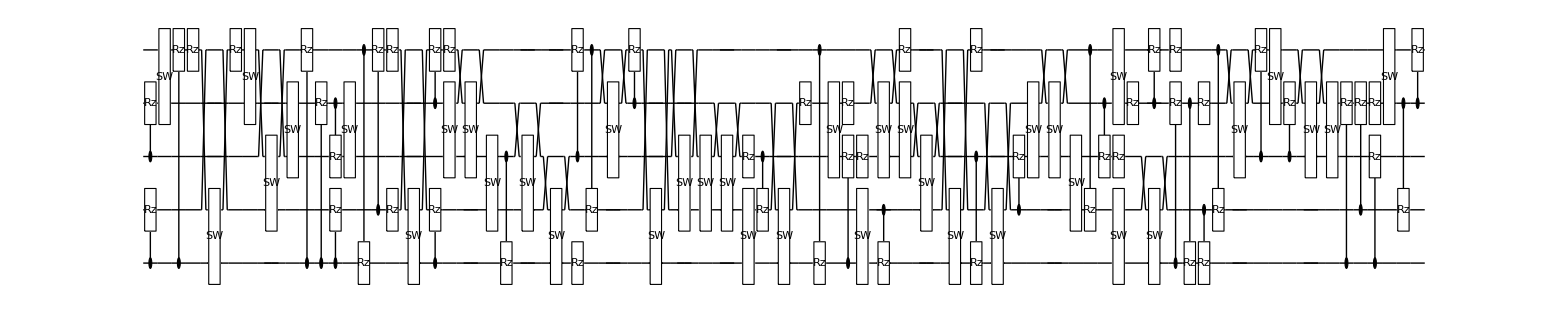

**** Compile @Sun 18 Dec 2022 11:26:27 τ=18.4; δ0.2 ****

Cycle 1@Sun 18 Dec 2022 11:31:55 completed with ngates=35, cost=0.00003318658083428794, at eval=1592

Cycle 2@Sun 18 Dec 2022 11:37:58 completed with ngates=39, cost=7.281283692539553e-6, at eval=3421

Cycle 3@Sun 18 Dec 2022 11:43:00 completed with ngates=42, cost=4.987630529695863e-7, at eval=4783

Cycle 4@Sun 18 Dec 2022 11:45:13 adjust hyperparams, slowdown:True

Cycle 5@Sun 18 Dec 2022 11:56:39 completed with ngates=61, cost=4.055480118392296e-8, at eval=6957

Cycle 6@Sun 18 Dec 2022 12:03:27 adjust hyperparams, slowdown:True

Cycle 7@Sun 18 Dec 2022 12:19:01 adjust hyperparams, slowdown:True

Cycle 8@Sun 18 Dec 2022 12:22:37 adjust hyperparams, slowdown:False

Cycle 9@Sun 18 Dec 2022 12:26:17 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=4.05548×10^-8

τ=18.6; δ=0.2; cost=4.05548×10^-8; ngates=61; runtime=63.15 min

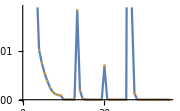

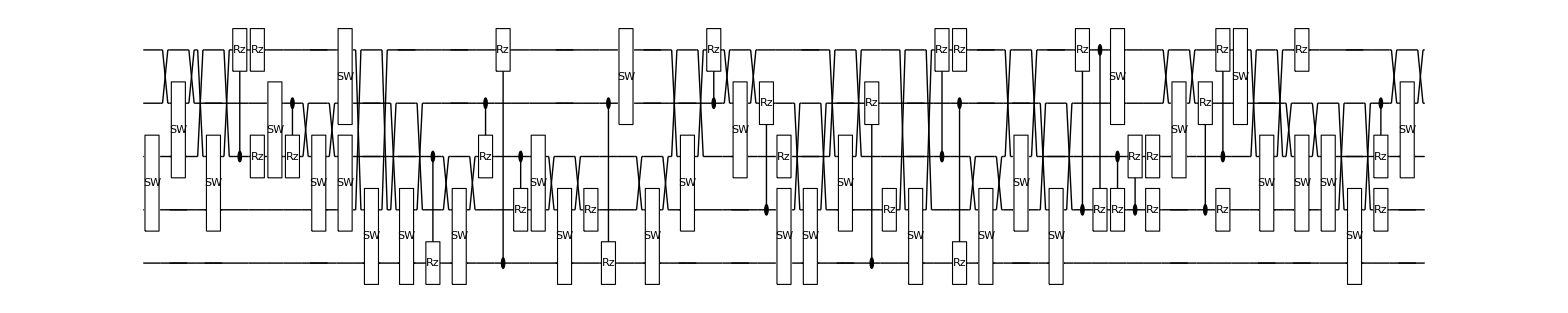

**** Compile @Sun 18 Dec 2022 12:29:38 τ=18.6; δ0.2 ****

Cycle 1@Sun 18 Dec 2022 12:35:46 completed with ngates=43, cost=0.00011315316115756424, at eval=1682

Cycle 2@Sun 18 Dec 2022 12:41:07 completed with ngates=39, cost=4.140410673536543e-6, at eval=3020

Cycle 3@Sun 18 Dec 2022 12:43:21 adjust hyperparams, slowdown:True

Cycle 4@Sun 18 Dec 2022 12:52:35 completed with ngates=47, cost=7.104491852594208e-7, at eval=5018

Cycle 5@Sun 18 Dec 2022 12:57:59 adjust hyperparams, slowdown:True

Cycle 6@Sun 18 Dec 2022 13:11:20 adjust hyperparams, slowdown:True

Cycle 7@Sun 18 Dec 2022 13:20:10 completed with ngates=49, cost=1.3355520200875048e-7, at eval=8243

Cycle 8@Sun 18 Dec 2022 13:22:55 adjust hyperparams, slowdown:False

Cycle 9@Sun 18 Dec 2022 13:25:47 adjust hyperparams, slowdown:False

Cycle 10@Sun 18 Dec 2022 13:28:46 adjust hyperparams, slowdown:False

Cycle 11@Sun 18 Dec 2022 13:31:50 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.33555×10^-7

τ=18.8; δ=0.2; cost=1.33555×10^-7; ngates=49; runtime=64.3083 min

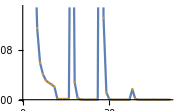

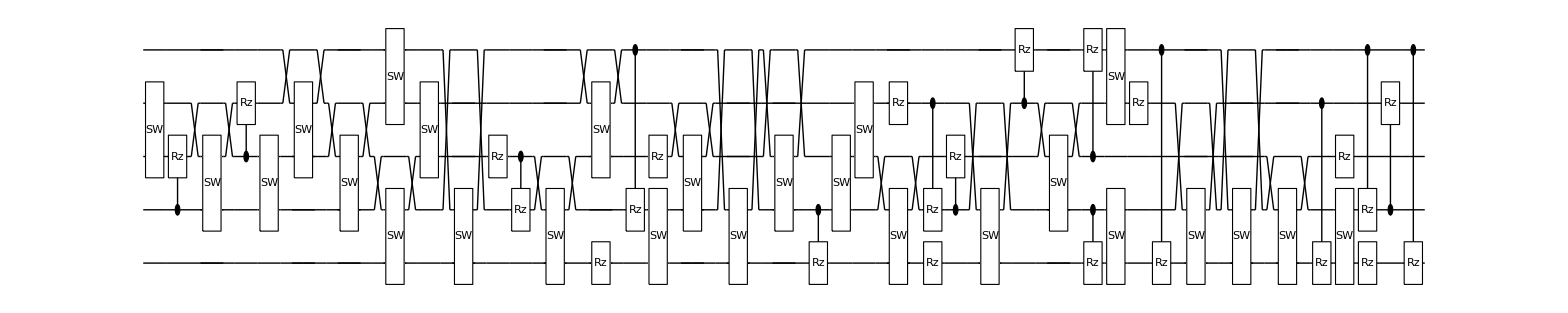

**** Compile @Sun 18 Dec 2022 13:33:58 τ=18.8; δ0.2 ****

Cycle 1@Sun 18 Dec 2022 13:38:23 completed with ngates=28, cost=0.0001003191828511385, at eval=1341

Cycle 2@Sun 18 Dec 2022 13:41:37 completed with ngates=37, cost=3.4260923033047064e-6, at eval=2474

Cycle 3@Sun 18 Dec 2022 13:46:41 completed with ngates=47, cost=5.177064895667272e-7, at eval=3795

Cycle 4@Sun 18 Dec 2022 13:54:50 completed with ngates=62, cost=1.0450727261357429e-7, at eval=5290

Cycle 5@Sun 18 Dec 2022 14:07:25 completed with ngates=75, cost=7.334668994385396e-8, at eval=6984

Cycle 6@Sun 18 Dec 2022 14:11:36 adjust hyperparams, slowdown:True

Cycle 7@Sun 18 Dec 2022 14:19:59 adjust hyperparams, slowdown:True

Cycle 8@Sun 18 Dec 2022 14:39:00 adjust hyperparams, slowdown:True

Cycle 9@Sun 18 Dec 2022 15:00:01 completed with ngates=86, cost=2.9643639876120176e-8, at eval=10591

Cycle 10@Sun 18 Dec 2022 15:06:25 adjust hyperparams, slowdown:False

Cycle 11@Sun 18 Dec 2022 15:34:44 completed with ngates=96, cost=4.38804959035366e-9, at eval=13083

Cycle 12@Sun 18 Dec 2022 15:43:05 adjust hyperparams, slowdown:False

Cycle 13@Sun 18 Dec 2022 15:51:30 adjust hyperparams, slowdown:False

Cycle 14@Sun 18 Dec 2022 15:59:36 adjust hyperparams, slowdown:False

Cycle 15@Sun 18 Dec 2022 16:27:02 completed with ngates=100, cost=3.086910171923307e-9, at eval=16868

Cycle 16@Sun 18 Dec 2022 16:35:29 adjust hyperparams, slowdown:False

Cycle 17@Sun 18 Dec 2022 16:44:27 adjust hyperparams, slowdown:False

Cycle 18@Sun 18 Dec 2022 16:53:52 adjust hyperparams, slowdown:False

Cycle 19@Sun 18 Dec 2022 17:03:40 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=3.08691×10^-9

τ=19.; δ=0.2; cost=3.08691×10^-9; ngates=100; runtime=247.4 min

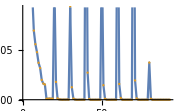

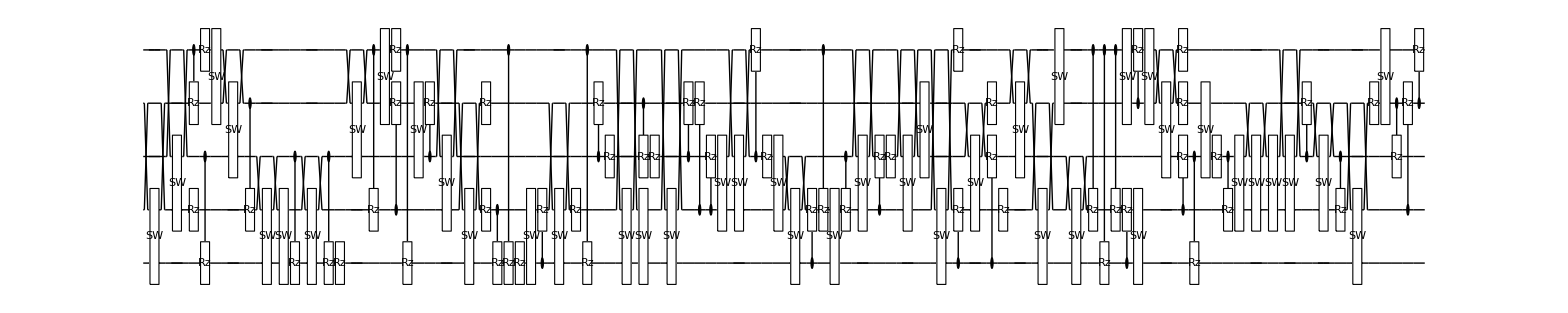

**** Compile @Sun 18 Dec 2022 17:41:24 τ=19.; δ0.2 ****

Cycle 1@Sun 18 Dec 2022 17:46:57 completed with ngates=39, cost=1.0396765243170236e-6, at eval=1613

Cycle 2@Sun 18 Dec 2022 17:48:58 adjust hyperparams, slowdown:True

Cycle 3@Sun 18 Dec 2022 17:53:00 adjust hyperparams, slowdown:True

Cycle 4@Sun 18 Dec 2022 18:16:15 completed with ngates=59, cost=4.217612448176311e-8, at eval=5156

Cycle 5@Sun 18 Dec 2022 18:32:49 adjust hyperparams, slowdown:True

Cycle 6@Sun 18 Dec 2022 18:36:29 adjust hyperparams, slowdown:False

Cycle 7@Sun 18 Dec 2022 18:40:22 adjust hyperparams, slowdown:False

Cycle 8@Sun 18 Dec 2022 18:44:25 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=4.21761×10^-8

τ=19.2; δ=0.2; cost=4.21761×10^-8; ngates=59; runtime=66.0869 min

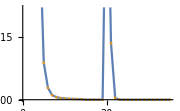

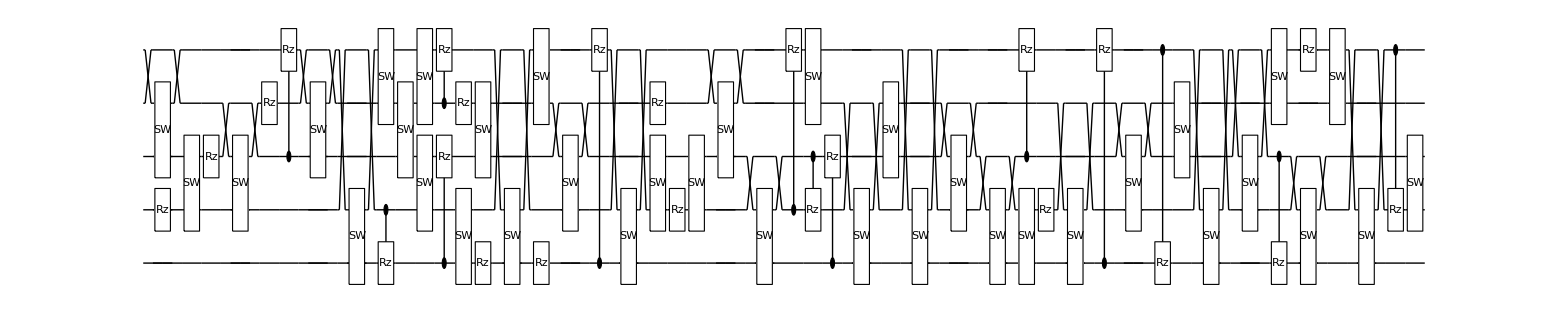

**** Compile @Sun 18 Dec 2022 18:47:29 τ=19.2; δ0.2 ****

Cycle 1@Sun 18 Dec 2022 18:53:04 completed with ngates=36, cost=0.00022264314117559358, at eval=1615

Cycle 2@Sun 18 Dec 2022 18:57:04 completed with ngates=37, cost=8.977136595422763e-6, at eval=2900

Cycle 3@Sun 18 Dec 2022 19:02:33 completed with ngates=48, cost=2.6880051584576847e-7, at eval=4275

Cycle 4@Sun 18 Dec 2022 19:05:09 adjust hyperparams, slowdown:True

Cycle 5@Sun 18 Dec 2022 19:10:29 adjust hyperparams, slowdown:True

Cycle 6@Sun 18 Dec 2022 19:23:34 adjust hyperparams, slowdown:True

Cycle 7@Sun 18 Dec 2022 19:26:12 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=2.68801×10^-7

τ=19.4; δ=0.2; cost=2.68801×10^-7; ngates=48; runtime=40.3871 min

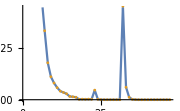

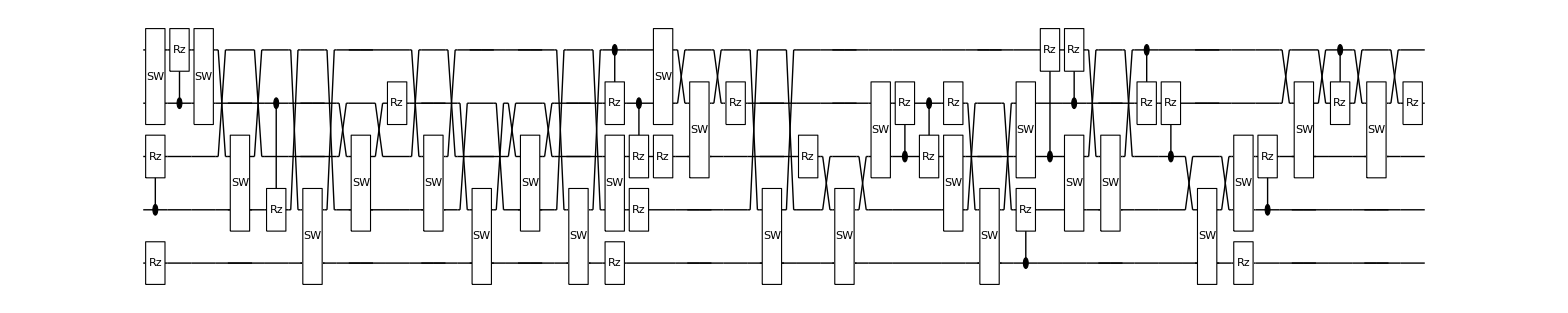

**** Compile @Sun 18 Dec 2022 19:27:59 τ=19.4; δ0.2 ****

Cycle 1@Sun 18 Dec 2022 19:32:45 completed with ngates=33, cost=0.000031948011974369805, at eval=1395

Cycle 2@Sun 18 Dec 2022 19:36:28 completed with ngates=38, cost=5.8553194135502196e-6, at eval=2568

Cycle 3@Sun 18 Dec 2022 19:38:26 adjust hyperparams, slowdown:True

Cycle 4@Sun 18 Dec 2022 19:49:03 completed with ngates=49, cost=9.987113380738322e-7, at eval=4999

Cycle 5@Sun 18 Dec 2022 20:03:20 completed with ngates=56, cost=2.986050762210368e-8, at eval=7179

Cycle 6@Sun 18 Dec 2022 20:09:16 adjust hyperparams, slowdown:True

Cycle 7@Sun 18 Dec 2022 20:24:05 adjust hyperparams, slowdown:True

Cycle 8@Sun 18 Dec 2022 20:27:17 adjust hyperparams, slowdown:False

Cycle 9@Sun 18 Dec 2022 20:30:41 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=2.98605×10^-8

τ=19.6; δ=0.2; cost=2.98605×10^-8; ngates=56; runtime=65.0216 min

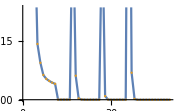

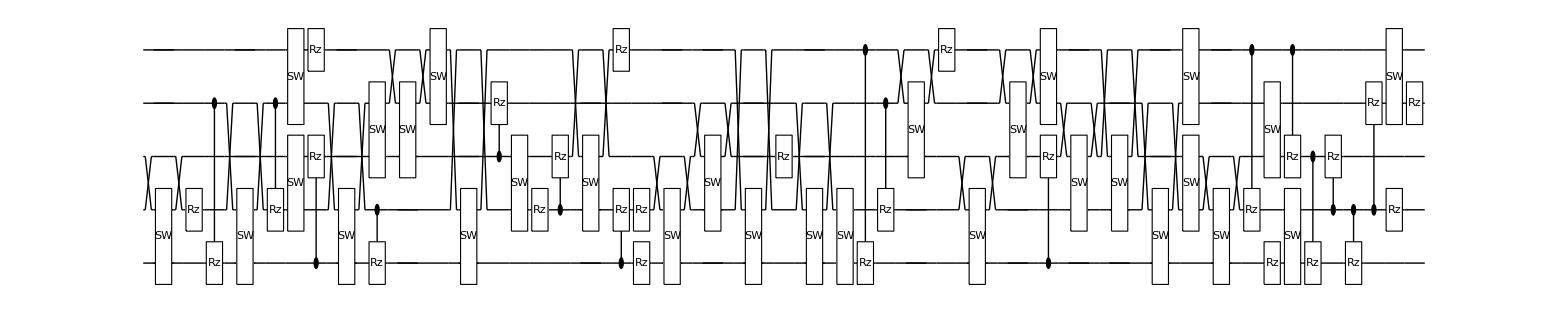

**** Compile @Sun 18 Dec 2022 20:33:06 τ=19.6; δ0.2 ****

Cycle 1@Sun 18 Dec 2022 20:38:49 completed with ngates=40, cost=4.044251952328715e-6, at eval=1590

Cycle 2@Sun 18 Dec 2022 20:40:56 adjust hyperparams, slowdown:True

Cycle 3@Sun 18 Dec 2022 20:51:12 completed with ngates=47, cost=7.124790865065123e-7, at eval=3997

Cycle 4@Sun 18 Dec 2022 21:05:11 completed with ngates=71, cost=5.3655406118124915e-8, at eval=5802

Cycle 5@Sun 18 Dec 2022 21:13:24 adjust hyperparams, slowdown:True

Cycle 6@Sun 18 Dec 2022 21:31:33 adjust hyperparams, slowdown:True

Cycle 7@Sun 18 Dec 2022 21:35:49 adjust hyperparams, slowdown:False

Cycle 8@Sun 18 Dec 2022 21:51:51 completed with ngates=82, cost=2.3911998159320547e-8, at eval=9410

Cycle 9@Sun 18 Dec 2022 22:12:49 completed with ngates=92, cost=1.7157364418096677e-9, at eval=11371

Cycle 10@Sun 18 Dec 2022 22:19:22 adjust hyperparams, slowdown:False

Cycle 11@Sun 18 Dec 2022 22:26:15 adjust hyperparams, slowdown:False

Cycle 12@Sun 18 Dec 2022 22:33:14 adjust hyperparams, slowdown:False

Cycle 13@Sun 18 Dec 2022 22:40:42 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.71574×10^-9

τ=19.8; δ=0.2; cost=1.71574×10^-9; ngates=92; runtime=135.465 min

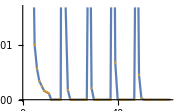

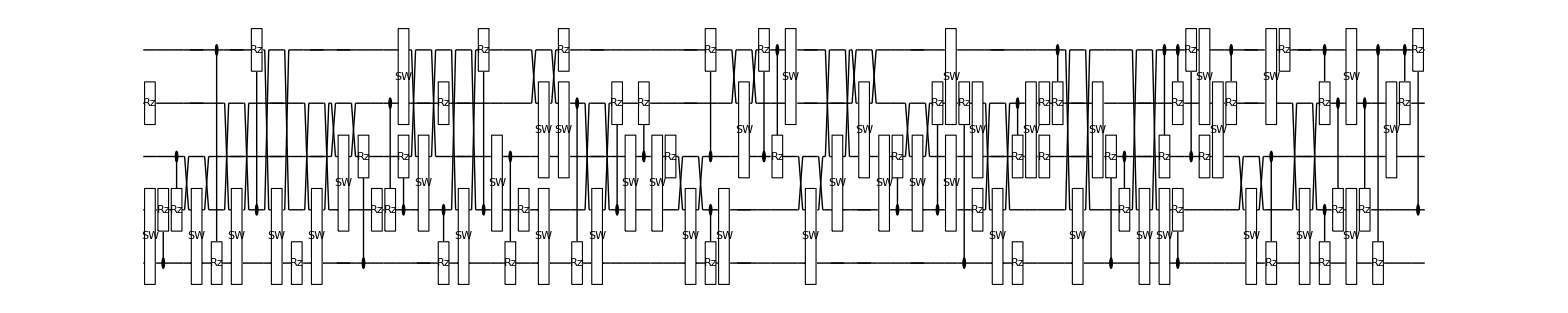

**** Compile @Sun 18 Dec 2022 22:48:40 τ=19.8; δ0.2 ****

Cycle 1@Sun 18 Dec 2022 22:57:02 completed with ngates=46, cost=3.3018347580515695e-6, at eval=2275

Cycle 2@Sun 18 Dec 2022 22:59:36 adjust hyperparams, slowdown:True

Cycle 3@Sun 18 Dec 2022 23:04:58 adjust hyperparams, slowdown:True

Cycle 4@Sun 18 Dec 2022 23:17:06 adjust hyperparams, slowdown:True

Cycle 5@Sun 18 Dec 2022 23:19:44 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=3.30183×10^-6

τ=20.; δ=0.2; cost=3.30183×10^-6; ngates=46; runtime=32.6496 min

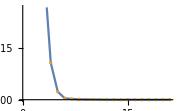

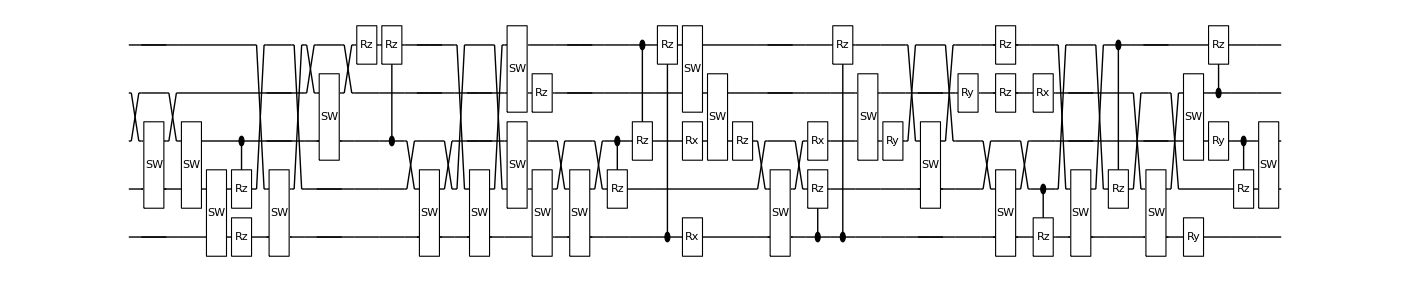

**** Compile @Sun 18 Dec 2022 23:21:26 τ=20.; δ3.5 ****

Cycle 1@Sun 18 Dec 2022 23:26:47 completed with ngates=40, cost=0.0001104195092745952, at eval=1553

Cycle 2@Sun 18 Dec 2022 23:28:46 adjust hyperparams, slowdown:True

Cycle 3@Sun 18 Dec 2022 23:37:45 completed with ngates=42, cost=0.000014335612921190233, at eval=3951

Cycle 4@Sun 18 Dec 2022 23:48:05 completed with ngates=45, cost=1.4169885498294121e-6, at eval=5954

Cycle 5@Mon 19 Dec 2022 00:03:21 completed with ngates=58, cost=2.4074627091863476e-7, at eval=8236

Cycle 6@Mon 19 Dec 2022 00:09:46 adjust hyperparams, slowdown:True

Cycle 7@Mon 19 Dec 2022 00:25:01 adjust hyperparams, slowdown:True

Cycle 8@Mon 19 Dec 2022 00:37:01 completed with ngates=73, cost=1.1637013908050164e-8, at eval=11241

Cycle 9@Mon 19 Dec 2022 00:41:27 adjust hyperparams, slowdown:False

Cycle 10@Mon 19 Dec 2022 00:46:05 adjust hyperparams, slowdown:False

Cycle 11@Mon 19 Dec 2022 00:50:49 adjust hyperparams, slowdown:False

Cycle 12@Mon 19 Dec 2022 00:55:42 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.1637×10^-8

τ=23.5; δ=3.5; cost=1.1637×10^-8; ngates=73; runtime=98.9093 min

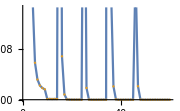

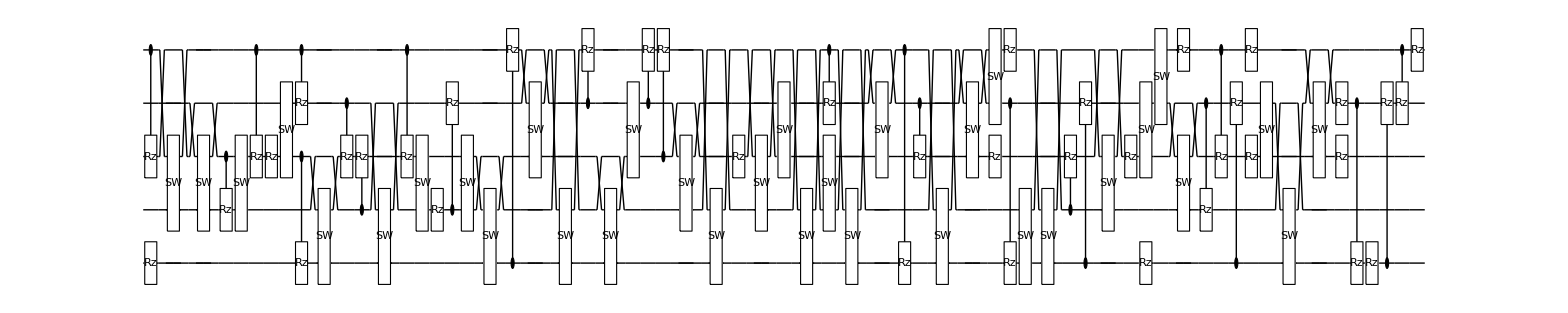

**** Compile @Mon 19 Dec 2022 01:00:26 τ=23.5; δ3.5 ****

Cycle 1@Mon 19 Dec 2022 01:05:28 completed with ngates=33, cost=8.738601144586688e-6, at eval=1469

Cycle 2@Mon 19 Dec 2022 01:07:23 adjust hyperparams, slowdown:True

Cycle 3@Mon 19 Dec 2022 01:16:23 completed with ngates=45, cost=1.420646943528503e-6, at eval=3834

Cycle 4@Mon 19 Dec 2022 01:32:24 completed with ngates=46, cost=2.5422920713058517e-7, at eval=6991

Cycle 5@Mon 19 Dec 2022 01:37:42 adjust hyperparams, slowdown:True

Cycle 6@Mon 19 Dec 2022 01:50:31 adjust hyperparams, slowdown:True

Cycle 7@Mon 19 Dec 2022 01:53:03 adjust hyperparams, slowdown:False

Cycle 8@Mon 19 Dec 2022 01:55:39 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=2.54229×10^-7

τ=27.; δ=3.5; cost=2.54229×10^-7; ngates=46; runtime=56.7332 min

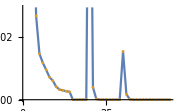

-Graphics-

#### Results and analysis

```mathematica
rexactot2<<rexactot2.mx
```

Null rexactot2

```mathematica
bcscompile<<bcscompile.mx
```

bcscompile Null

```mathematica
(* get the best result with a treshold target *)
minRes[rescomp_,target_:10^-6]:=Module[{τ,δ,cres,idx,tidx=2,gidx=2},
cres=rescomp[[10]];
For[idx=2,idx<=Length@cres["E"],idx++,
If[cres["E"][[idx]]<=target,
tidx=idx;
Break[]
]
];
gidx=Last@Ordering[Length/@cres["ansatz"],2];
If[cres["E"][[gidx]]<=target,
{cres["ansatz"][[gidx]],cres["θvars"][[gidx]]}
,
{cres["ansatz"][[tidx]],cres["θvars"][[tidx]]}
]

]
```

The matrixExp vs compiled

```mathematica
CustomGatesDefinitions={Subscript[SW, index1_,index2_][θ_]:>Subscript[U, index1,index2][{{1,0,0,0},{0,ⅇ^((ⅈ θ)/2)Cos[θ/2],-ⅈ ⅇ^((ⅈ θ)/2)Sin[θ/2],0 },{0,-ⅈ ⅇ^((ⅈ θ)/2)Sin[θ/2], ⅇ^((ⅈ θ)/2)Cos[θ/2],0 },{0,0,0,1}}]
,
Subscript[CRx, e_,n_][θ_]:>Subscript[U, e,n][{{Cos[θ/2],0,-I Sin[θ/2],0},{0,Cos[θ/2],0,I Sin[θ/2]},{-I Sin[θ/2],0,Cos[θ/2],0},{0,I Sin[θ/2],0,Cos[θ/2]}}]
,
	Subscript[CRy, e_,n_][θ_]:>Subscript[U, e,n][{{Cos[θ/2],0,-Sin[θ/2],0},{0,Cos[θ/2],0,Sin[θ/2]},{Sin[θ/2],0,Cos[θ/2],0},{0,-Sin[θ/2],0,Cos[θ/2]}}]	
}; 
CustomGatesDraw={Subscript[SW, index1_,index2_][_]:>Subscript[SWAP, index1,index2]};
```

```mathematica
(*initialisation*)
{ψexact,ψinitexact}=CreateQuregs[5,2];
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
SetQuregMatrix[ψinitexact,initv];
```

```mathematica
CloneQureg[ψexact,ψinitexact];
rexactcomp={{0,1}};
summary=Table[
{τ,δ,res}=comp;
{ansatz,θvars}=minRes[res,10^-6];
ApplyCircuit[ψexact,ansatz/.CustomGatesDefinitions/.θvars];
AppendTo[rexactcomp,{τ,CalcFidelity[ψexact,ψinitexact]}];
<|"ngates"->Length@ansatz,"ansatz"->ansatz,"θvars"->θvars,"time"->res[[1]],"cost"->res[[2]]|>
,{comp, bcscompile}];
```

```mathematica
ListPlot[{rexactot2,rexactcomp},Joined->{True,True},PlotStyle->{Thick,Dashed},PlotTheme->"Detailed",AspectRatio->0.3,PlotLabel->"Rexact(τ)",ImageSize->Large,FrameTicks->{{Range[1,1.55,0.05],None},{Automatic,None}},PlotLegends->{"MatrixExp","Compilation"}]
```

-Graphics-

```mathematica
Histogram[summary[[All,"ngates"]],10,ChartLabels->{"Number of gates"},PlotTheme->"Detailed"]
```

-Graphics-

#### Converting to NVC native gates

```mathematica
Options[NVCenterDelft]={
qubitsNum->6,
T1-> <|0-> 3600,1->60,2->60,3->60,4->60,5->60 |>,
T2-> <|0-> 1.5,1->10,2->10,3->10,4->9,5->9|>,
GlobalField-><|#->RandomReal[{-0.01,0.01}]&/@Range[0,5]|>,
GlobalFieldDetuning->66000,
FreqSingleXY-> <|0->15*10^6,1->500 ,2->500,3->500,4->500,5->500|>,
FreqSingleZ-><|0->32*10^6,1->400*10^3,2->400*10^3,3->400*10^3,4->400*10^3,5->400*10^3|>,
FreqCRot-> <|1-> 1.5*10^3,2->2.8*10^3,3->0.8*10^3,4->2*10^3 ,5->2*10^3|>,
FidCRot-><|1-> 0.98,2->0.98, 3->0.98,4->0.98 ,5->0.98|>,
FidSingleXY-> <| 0->0.9995,1-> 0.995,2->0.995, 3->0.99,4->0.99,5->0.99 |>,
FidSingleZ->  <| 0->0.9999,1-> 0.9999,2->0.99999, 3->0.9999,4->0.999,6->0.99 |>,
EFSingleXY->{0.75,0.25},
EFCRot->{0.9,0.1},
FidInit-> 0.999,
DurInit->2*10^-3,
FidMeas->0.946,
DurMeas->2*10^-5
};
```

```mathematica
dev=NVCenterDelft[];
```

```mathematica
dev[Gates][[All,1]]
```

{Init_(VQD`Private`q$_)/;VQD`Private`q$===0,M_(VQD`Private`q$_)/;VQD`Private`q$===0,Wait_(VQD`Private`qubits$__)[VQD`Private`dur$_],Rz_(VQD`Private`q$_)[VQD`Private`θ$_],Rx_(VQD`Private`q$_)[VQD`Private`θ$_]/;VQD`Private`q$===0,Ry_(VQD`Private`q$_)[VQD`Private`θ$_]/;VQD`Private`q$===0,Rx_(VQD`Private`q$_)[VQD`Private`θ$_]/;VQD`Private`q$>0,Ry_(VQD`Private`q$_)[VQD`Private`θ$_]/;VQD`Private`q$>0,CRx_(VQD`Private`e$_,VQD`Private`n$_)[VQD`Private`θ$_]/;VQD`Private`e$==0&&VQD`Private`n$>0,CRy_(VQD`Private`e$_,VQD`Private`n$_)[VQD`Private`θ$_]/;VQD`Private`e$==0&&VQD`Private`n$>0}

#### Convert C[Rz(θ)] and SW[θ] to native NVC gates

```mathematica
CustomGatesDefinitions
```

{SW_(index1_,index2_)[θ_]:>U_(index1,index2)[{{1,0,0,0},{0,ⅇ^((ⅈ θ)/2) Cos[θ/2],-ⅈ ⅇ^((ⅈ θ)/2) Sin[θ/2],0},{0,-ⅈ ⅇ^((ⅈ θ)/2) Sin[θ/2],ⅇ^((ⅈ θ)/2) Cos[θ/2],0},{0,0,0,1}}],CRx_(e_,n_)[θ_]:>U_(e,n)[{{Cos[θ/2],0,-ⅈ Sin[θ/2],0},{0,Cos[θ/2],0,ⅈ Sin[θ/2]},{-ⅈ Sin[θ/2],0,Cos[θ/2],0},{0,ⅈ Sin[θ/2],0,Cos[θ/2]}}],CRy_(e_,n_)[θ_]:>U_(e,n)[{{Cos[θ/2],0,-Sin[θ/2],0},{0,Cos[θ/2],0,Sin[θ/2]},{Sin[θ/2],0,Cos[θ/2],0},{0,-Sin[θ/2],0,Cos[θ/2]}}]}

```mathematica
tonvcnative={
Subscript[C, 0][Subscript[Rx, t_][θ_]]:>Sequence@@{Subscript[CRx, 0,t][-θ/2],Subscript[Rx, t][θ/2]},
Subscript[C, 0][Subscript[Rz, t_][θ_]]:>Sequence@@{Subscript[Ry, t][π/2],Subscript[CRx, 0,t][-θ/2],Subscript[Rx, t][θ/2],Subscript[Ry, t][-π/2]}
};
```

```mathematica
MatrixForm[CalcCircuitMatrix[Subscript[Rx, 0][-π/2]]]
```

(1/(√2) | ⅈ/(√2)
ⅈ/(√2) | 1/(√2))

```mathematica
sw={Subscript[C, 0][Subscript[X, 1]],Subscript[Rz, 1][θ/2],Subscript[C, 0][Subscript[X, 1]],Subscript[H, 1],Subscript[H, 0],Subscript[C, 0][Subscript[X, 1]],Subscript[Rz, 1][θ/2],Subscript[C, 0][Subscript[X, 1]],Subscript[H, 0],Subscript[H, 1],Subscript[Rx, 0][-π/2],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[X, 1]],Subscript[Rz, 1][θ/2],Subscript[C, 0][Subscript[X, 1]],Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2]};
DrawCircuit[sw]
MatrixForm[TrigReduce[ComplexExpand[ⅇ^(ⅈ θ/4)Simplify[CalcCircuitMatrix[sw/.CustomGatesDefinitions],Reals[θ]]]]]
```

-Graphics-

(1 | 0 | 0 | 0
0 | 1/2 (1+Cos[θ]+ⅈ Sin[θ]) | 1/2 (1-Cos[θ]-ⅈ Sin[θ]) | 0
0 | 1/2 (1-Cos[θ]-ⅈ Sin[θ]) | 1/2 (1+Cos[θ]+ⅈ Sin[θ]) | 0
0 | 0 | 0 | 1)

```mathematica
MatrixForm[TrigReduce@ComplexExpand@CalcCircuitMatrix[Subscript[SW, 1,0][θ]/.CustomGatesDefinitions]]
```

(1 | 0 | 0 | 0
0 | 1/2 (1+Cos[θ]+ⅈ Sin[θ]) | 1/2 (1-Cos[θ]-ⅈ Sin[θ]) | 0
0 | 1/2 (1-Cos[θ]-ⅈ Sin[θ]) | 1/2 (1+Cos[θ]+ⅈ Sin[θ]) | 0
0 | 0 | 0 | 1)

```mathematica
sw={Subscript[C, 0][Subscript[Rx, 1][π]],Subscript[Rz, 1][θ],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[Rx, 1][π]],Subscript[Rz, 1][θ],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[Rx, 1][π]],Subscript[Ry, 0][-π/2],Subscript[Rz, 1][θ],Subscript[C, 0][Subscript[Rx, 1][π]],Subscript[Rx, 0][π/2]};
DrawCircuit[sw]
TrigReduce@ComplexExpand@Simplify[ⅇ^(ⅈ θ/2) CalcCircuitMatrix[sw/.CustomGatesDefinitions],Reals[θ]]
```

-Graphics-

{{(1/4+ⅈ/4) (ⅈ+Cos[θ]-Sin[θ]),1/4 (-1-(1+ⅈ) Cos[θ]+ⅈ Cos[2 θ]+(1-ⅈ) Sin[θ]-Sin[2 θ]),1/4 ⅈ (1+(1+ⅈ) Cos[θ]-ⅈ Cos[2 θ]-(1-ⅈ) Sin[θ]+Sin[2 θ]),(1/4-ⅈ/4) (ⅈ+Cos[θ]-Sin[θ])},{(-1/4-ⅈ/4) (-ⅈ+Cos[θ]+Sin[θ]),1/4 (ⅈ+(1+ⅈ) Cos[θ]-Cos[2 θ]-(1-ⅈ) Sin[θ]-ⅈ Sin[2 θ]),-1/4 ⅈ (ⅈ+(1+ⅈ) Cos[θ]-Cos[2 θ]-(1-ⅈ) Sin[θ]-ⅈ Sin[2 θ]),(-1/4+ⅈ/4) (-ⅈ+Cos[θ]+Sin[θ])},{(1/4+ⅈ/4) (ⅈ+Cos[θ]-Sin[θ]),1/4 (1+(1+ⅈ) Cos[θ]-ⅈ Cos[2 θ]-(1-ⅈ) Sin[θ]+Sin[2 θ]),1/4 ⅈ (1+(1+ⅈ) Cos[θ]-ⅈ Cos[2 θ]-(1-ⅈ) Sin[θ]+Sin[2 θ]),(-1/4+ⅈ/4) (ⅈ+Cos[θ]-Sin[θ])},{(1/4+ⅈ/4) (-ⅈ+Cos[θ]+Sin[θ]),1/4 (ⅈ+(1+ⅈ) Cos[θ]-Cos[2 θ]-(1-ⅈ) Sin[θ]-ⅈ Sin[2 θ]),1/4 ⅈ (ⅈ+(1+ⅈ) Cos[θ]-Cos[2 θ]-(1-ⅈ) Sin[θ]-ⅈ Sin[2 θ]),(-1/4+ⅈ/4) (-ⅈ+Cos[θ]+Sin[θ])}}

```mathematica
TrigReduce@ComplexExpand@Simplify[1/4 ⅈ ⅇ^(-(ⅈ θ)/2) (ⅈ-(1-ⅈ) ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)),Reals[θ]]
```

1/4 ((-2-ⅈ) Cos[θ/2]+ⅈ Cos[(3 θ)/2]+Sin[θ/2]-Sin[(3 θ)/2])

```mathematica
MatrixForm[CalcCircuitMatrix[Subscript[SW, 1,0][θ]/.CustomGatesDefinitions]]
MatrixForm[ⅇ^(ⅈ θ/2)Simplify[ⅇ^(-ⅈ θ/4)*CalcCircuitMatrix[{R[θ/2,Subscript[Y, 0] Subscript[Y, 1]],R[θ/2,Subscript[X, 0] Subscript[X, 1]],R[θ/2,Subscript[Z, 0] Subscript[Z, 1]]}],Reals[θ]]]
MatrixForm[Simplify[CalcCircuitMatrix[{R[θ/2,Subscript[Y, 0] Subscript[Y, 1]],R[θ/2,Subscript[X, 0] Subscript[X, 1]],R[θ/2,Subscript[Z, 0] Subscript[Z, 1]]}],Reals[θ]]]
```

(1 | 0 | 0 | 0
0 | ⅇ^((ⅈ θ)/2) Cos[θ/2] | -ⅈ ⅇ^((ⅈ θ)/2) Sin[θ/2] | 0
0 | -ⅈ ⅇ^((ⅈ θ)/2) Sin[θ/2] | ⅇ^((ⅈ θ)/2) Cos[θ/2] | 0
0 | 0 | 0 | 1)

(1 | 0 | 0 | 0
0 | ⅇ^((ⅈ θ)/2) Cos[θ/2] | -ⅈ ⅇ^((ⅈ θ)/2) Sin[θ/2] | 0
0 | -ⅈ ⅇ^((ⅈ θ)/2) Sin[θ/2] | ⅇ^((ⅈ θ)/2) Cos[θ/2] | 0
0 | 0 | 0 | 1)

(ⅇ^(-(ⅈ θ)/4) | 0 | 0 | 0
0 | 1/2 ⅇ^(-(ⅈ θ)/4) (1+ⅇ^(ⅈ θ)) | -ⅈ ⅇ^((ⅈ θ)/4) Sin[θ/2] | 0
0 | -ⅈ ⅇ^((ⅈ θ)/4) Sin[θ/2] | 1/2 ⅇ^(-(ⅈ θ)/4) (1+ⅇ^(ⅈ θ)) | 0
0 | 0 | 0 | ⅇ^(-(ⅈ θ)/4))

```mathematica
MatrixForm[ExpandAll[CalcCircuitMatrix[{Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[Rx, 1][π]],Subscript[Rx, 1][π/2]}]]]
MatrixForm[CalcCircuitMatrix[{Subscript[C, 0][Subscript[Rx, 1][π]]}]]
```

(1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | 1 | 0
0 | -ⅈ | 0 | 0)

(1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | 1 | 0
0 | -ⅈ | 0 | 0)

```mathematica
MatrixForm[CalcCircuitMatrix[{Subscript[Rz, 1][θ],Subscript[C, 0][Subscript[X, 1]]}]]
MatrixForm[CalcCircuitMatrix[{Subscript[C, 0][Subscript[X, 1]],Subscript[Rz, 1][θ]}]]
```

(ⅇ^(-(ⅈ θ)/2) | 0 | 0 | 0
0 | 0 | 0 | ⅇ^((ⅈ θ)/2)
0 | 0 | ⅇ^((ⅈ θ)/2) | 0
0 | ⅇ^(-(ⅈ θ)/2) | 0 | 0)

(ⅇ^(-(ⅈ θ)/2) | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(-(ⅈ θ)/2)
0 | 0 | ⅇ^((ⅈ θ)/2) | 0
0 | ⅇ^((ⅈ θ)/2) | 0 | 0)

```mathematica
MatrixForm@CalcCircuitMatrix[{Subscript[Rz, 0][-π/2],Subscript[C, 0][Subscript[X, 1]]}]
MatrixForm@CalcCircuitMatrix[{Subscript[C, 0][Subscript[X, 1]],Subscript[Rz, 0][-π/2]}]
```

(ⅇ^((ⅈ π)/4) | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(-(ⅈ π)/4)
0 | 0 | ⅇ^((ⅈ π)/4) | 0
0 | ⅇ^(-(ⅈ π)/4) | 0 | 0)

(ⅇ^((ⅈ π)/4) | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(-(ⅈ π)/4)
0 | 0 | ⅇ^((ⅈ π)/4) | 0
0 | ⅇ^(-(ⅈ π)/4) | 0 | 0)

```mathematica
CalcCircuitMatrix[Subscript[Ph, 0][π/2]]
```

{{1,0},{0,ⅈ}}

```mathematica
MatrixForm@CalcCircuitMatrix[{Subscript[C, 0][Subscript[X, 1]]}]
MatrixForm[ⅇ^(ⅈ π/4) CalcCircuitMatrix[{Subscript[C, 0][Subscript[Rx, 1][π]],Subscript[Rz, 0][π/2]}]]
MatrixForm[ⅇ^(ⅈ π/4) CalcCircuitMatrix[{Subscript[Rz, 0][π/2],Subscript[C, 0][Subscript[Rx, 1][π]]}]]
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

```mathematica
zz=Chop@CalcPauliStringMatrix[Subscript[Z, 0] Subscript[Z, 1]]
```

{{1.,0,0,0},{0,-1.,0,0},{0,0,-1.,0},{0,0,0,1.}}

```mathematica
TrigReduce[ⅇ^(ⅇ^(ⅈ θ/2))]
```

ⅇ^(ⅇ^((ⅈ θ)/2))

```mathematica
ExpandAll@Chop@Simplify[MatrixExp[Cos[θ/2]*IdentityMatrix[4]+ⅈ Sin[θ/2]*zz],Reals[θ]]//MatrixForm
```

(ⅇ^(1. Cos[θ/2]+(0.+1. ⅈ) Sin[θ/2]) | 0 | 0 | 0
0 | ⅇ^(1. Cos[θ/2]-(0.+1. ⅈ) Sin[θ/2]) | 0 | 0
0 | 0 | ⅇ^(1. Cos[θ/2]-(0.+1. ⅈ) Sin[θ/2]) | 0
0 | 0 | 0 | ⅇ^(1. Cos[θ/2]+(0.+1. ⅈ) Sin[θ/2]))

```mathematica
{{1,0,0,0},{0,0,-1,0},{0,-1,0,0},{0,0,0,-1}}
```

```mathematica
MatrixForm@{{1,0,0,0},{0,ⅇ^((ⅈ θ)/2) Cos[θ/2],-ⅈ ⅇ^((ⅈ θ)/2) Sin[θ/2],0},{0,-ⅈ ⅇ^((ⅈ θ)/2) Sin[θ/2],ⅇ^((ⅈ θ)/2) Cos[θ/2],0},{0,0,0,1}}
```

(1 | 0 | 0 | 0
0 | ⅇ^((ⅈ θ)/2) Cos[θ/2] | -ⅈ ⅇ^((ⅈ θ)/2) Sin[θ/2] | 0
0 | -ⅈ ⅇ^((ⅈ θ)/2) Sin[θ/2] | ⅇ^((ⅈ θ)/2) Cos[θ/2] | 0
0 | 0 | 0 | 1)

```mathematica
DrawCircuit@%
```

-Graphics-

```mathematica
MatrixForm@CalcCircuitMatrix@{Subscript[Ry, 0][π/2]}
```

(1/(√2) | -1/(√2)
1/(√2) | 1/(√2))

```mathematica
swaprep={Subscript[SWAP, c_,t_]:>Sequence@@{Subscript[CRx, c,t][π/2],Subscript[Rx, t][π/2],Subscript[Rz, c][π/2],Subscript[CRx, c,t][π/2],Subscript[Rx, t][-π/2],Subscript[Rz, c][π/2],Subscript[CRx, c,t][π/2],Subscript[Rz, c][π/2],Subscript[Rx, t][π/2]}};
nvcnative={
Subscript[C, c_][Subscript[X, t_]]:>Sequence@@{swapCRx[Subscript[CRx, c,t][π/2]],Subscript[Rz, c][-π/2],Subscript[Rx, t][-π/2]},
Subscript[H, q_]:>Sequence@@{Subscript[Ry, q][π/2],Subscript[Rx, q][π]},
Subscript[CRx, c_,t_][θ_]:>swapCRx[Subscript[CRx, c,t][θ]]
};
```

```mathematica
(* minimize the rotation angle *)
round2pi[θ_]/;θ>=0:=With[{ϕ=Mod[θ,2π]},If[Abs[2π-ϕ]<ϕ,-(2π-ϕ),ϕ]]
replaceθ={
Subscript[Rz, q_][θ_]/;θ>=0:>Subscript[Rz, q][Chop@round2pi[θ]],
Subscript[Rx, q_][θ_]/;θ>=0:>Subscript[Rx, q][Chop@round2pi[θ]],
Subscript[Ry, q_][θ_]/;θ>=0:>Subscript[Ry, q][Chop@round2pi[θ]]
};
```

```mathematica
swapCRx[g_]:=Module[{i,j,θ,circ},
{i,j,θ}=g/.Subscript[CRx, p_,q_][t_]:>{p,q,t};
circ=Which[
(i==0)&&(j>0),
{Subscript[CRx, 0,j][θ]}
,
(i>0)&&(j>0)
,
{Subscript[SWAP, 0,i],Subscript[CRx, 0,j][θ],Subscript[SWAP, 0,i]}/.swaprep
,
(*i>0, j=0*)
True,
{Subscript[Ry, i][π/2],Subscript[Rx, i][π],Subscript[Ry, j][π/2],Subscript[Rx, j][π],Subscript[CRx, 0,i][θ],Subscript[Ry, i][π/2],Subscript[Rx, i][π],Subscript[Ry, j][π/2],Subscript[Rx, j][π]}
];
Sequence@@circ
]
```

```mathematica
(* simple gate merges *)
mergeNVCGates[longcirc_]:=Module[{circ,circcol,a,b,c,d,e,f,i,j,slen,k,l,θmerge={},deleted=0},
circ=longcirc;
While[True,
slen=Length@circ;
circcol=GetCircuitColumns[circ];
(* simplify parametric gates *)
circcol=circcol//.{
{a___,{b___,Subscript[Rx, j_][θ1_],c___},{d___,Subscript[Rx, j_][θ2_],e___},f___}:>{a,{b,Subscript[Rx, j][θ1+θ2],c},{d,e},f},
{a___,{b___,Subscript[Ry, j_][θ1_],c___},{d___,Subscript[Ry, j_][θ2_],e___},f___}:>{a,{b,Subscript[Ry, j][θ1+θ2],c},{d,e},f},
{a___,{b___,Subscript[Rz, j_][θ1_],c___},{d___,Subscript[Rz, j_][θ2_],e___},f___}:>{a,{b,Subscript[Rz, j][θ1+θ2],c},{d,e},f},
{a___,{b___,Subscript[CRx, i_,j_][θ1_],c___},{d___,Subscript[CRx, i_,j_][θ2_],e___},f___}:>{a,{b,Subscript[CRx, i,j][θ1+θ2],c},{d,e},f}
};
circ=DeleteElements[Flatten[circcol]/.replaceθ,{Subscript[_, __][0],Subscript[_, __][0.]}];
If[Length@circ==slen,Break[]];
];
circ
]
```